```mathematica
density[r_,p_]:=1/(r)^(p+3/2)Beta[r,p+1,3/2]/Beta[p+1,3/2];
rho[r_,p_]:=1/(r)^(p+3/2);
```

```mathematica
tPowerTicks[label_][min_,max_]:=Block[{min10,max10},min10=Floor[Log10[min]];
max10=Ceiling[Log10[max]];
Join[Table[{10^i,If[label,Superscript["10",i]]},{i,min10,max10}],Flatten[Table[{k 10^i,Spacer[{0,0}]},{i,min10,max10},{k,9}],1]]];
```

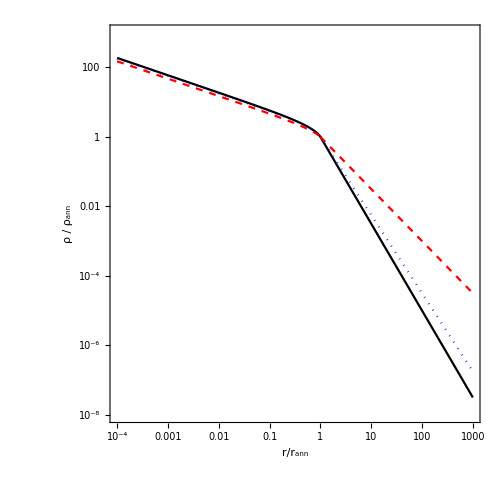

```mathematica
Show[LogLogPlot[density[r,1],{r,10^-4,1},PlotRange-> {{10^-4, 10^3},{10^-8, 10^3}},PlotStyle->Black,FrameTicks-> {{tPowerTicks[True][10^-8, 10^3],Automatic},{tPowerTicks[True][10^-4, 10^3],Automatic}}],LogLogPlot[rho[r,1],{r,1,10^3},PlotRange-> {{10^-4, 10^3},{10^-8, 10^3}},PlotStyle->Black] ,LogLogPlot[density[r,3/4],{r,10^-4,1},PlotRange-> {{10^-4, 10^3},{10^-8, 10^3}},PlotStyle->{Blue,Dotted}],LogLogPlot[rho[r,3/4],{r,1,10^3},PlotRange-> {{10^-4, 10^3},{10^-8, 10^3}},PlotStyle->{Blue,Dotted}],LogLogPlot[density[r,0],{r,10^-4,1},PlotRange-> {{10^-4, 10^3},{10^-8, 10^3}},PlotStyle->{Red,Dashed}],LogLogPlot[rho[r,0],{r,1,10^3},PlotRange-> {{10^-4, 10^3},{10^-8,10^3}},PlotStyle->{Red,Dashed}]
 ,Frame-> True,AspectRatio-> 1,FrameLabel-> {"r/r_ann", "ρ / ρ_ann"},LabelStyle-> Directive[Black,FontSize-> 25],FrameStyle-> Directive[Black,Thickness[0.0035]],ImageSize-> 500]
```

```mathematica
velocity[r_,p_]:=√2 √(Beta[r,p+1,5/2]/Beta[r,p+1,3/2]);
nu[r_,p_]:=√2 √(Beta[p+1,5/2]/Beta[p+1,3/2]);
```

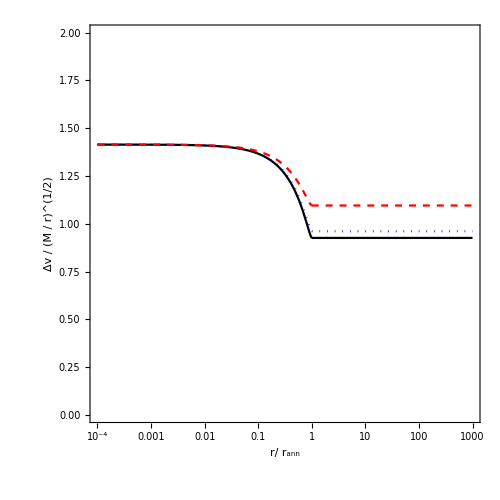

```mathematica
Show[LogLinearPlot[velocity[r,1],{r,10^-4,1},PlotRange-> {{10^-4, 10^3},{0, 2}},PlotStyle->Black,FrameTicks-> {{Automatic,Automatic},{tPowerTicks[True][10^-4, 10^3],Automatic}}],LogLinearPlot[nu[r,1],{r,1,10^3},PlotRange-> {{10^-4, 10^3},{0, 2}},PlotStyle->Black] ,LogLinearPlot[velocity[r,3/4],{r,10^-4,1},PlotRange-> {{10^-4, 10^3},{0, 2}},PlotStyle->{Blue,Dotted}],LogLinearPlot[nu[r,3/4],{r,1,10^3},PlotRange-> {{10^-4, 10^3},{0, 2}},PlotStyle->{Blue,Dotted}],LogLinearPlot[velocity[r,0],{r,10^-4,1},PlotRange-> {{10^-4, 10^3},{0, 2}},PlotStyle->{Red,Dashed}],LogLinearPlot[nu[r,0],{r,1,10^3},PlotRange-> {{10^-4, 10^3},{0,2}},PlotStyle->{Red,Dashed}]
 ,Frame-> True,AspectRatio-> 1,FrameLabel-> {"r/ r_ann","Δv / (M / r)^(1/2)"},LabelStyle-> Directive[Black,FontSize-> 25],FrameStyle-> Directive[Black,Thickness[0.0035]],ImageSize-> 500]
```

```mathematica
rbh=6 10^-7(*5 10^-8*);
rann=2.2 10^-3;
```

```mathematica
densitycone[r_,p_]:=1/r^(3/2+p)Integrate[t^p(√(1-t-rbh/r(1-rbh/r t))),{t,0,1/(1+rbh/r)}]/Integrate[t^p(√(1-t-rbh(1-rbh t))),{t,0,1/(1+rbh)}];
rhocone[r_,p_]:=1/r^(3/2+p)Integrate[t^p(√(1-t-rbh/r(1-rbh/r t))),{t,0,1/(1+rbh/rann)r/rann},GenerateConditions->False]/Integrate[t^p(√(1-t-rbh(1-rbh t))),{t,0,1/(1+rbh)}];
```

```mathematica
y1[r_]=densitycone[r,1];
z1[r_]=rhocone[r,1];
```

```mathematica
y2[r_]=densitycone[r,3/4];
z2[r_]=rhocone[r,3/4];
```

```mathematica
y3[r_]=densitycone[r,0];
z3[r_]=rhocone[r,0];
```

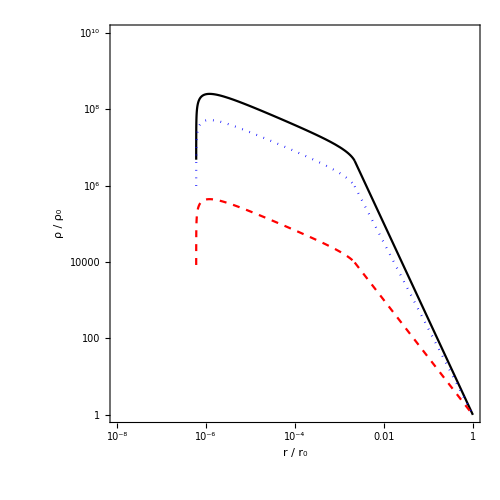

```mathematica
Show[LogLogPlot[y1[r],{r,rann,1},PlotRange->{{10^-8,1},{1, 10^10}},PlotStyle->Black,FrameTicks-> {{tPowerTicks[True][1,10^10],Automatic},{tPowerTicks[True][10^-8, 10^0],Automatic}}],LogLogPlot[z1[r],{r,10^-8,rann},PlotRange->{{10^-8,1},{1, 10^10}},PlotStyle->Black],LogLogPlot[y2[r],{r,rann,1},PlotRange->{{10^-8,1},{1, 10^10}},PlotStyle->{Blue,Dotted}],LogLogPlot[z2[r],{r,10^-8,rann},PlotRange->{{10^-8,1},{1, 10^10}},PlotStyle->{Blue,Dotted}],LogLogPlot[y3[r],{r,rann,1},PlotRange->{{10^-8,1},{1, 10^10}},PlotStyle->{Red,Dashed}],LogLogPlot[z3[r],{r,10^-8,rann},PlotRange->{{10^-8,1},{1, 10^10}},PlotStyle->{Red,Dashed}],AspectRatio-> 1,FrameLabel-> {"r / r_0","ρ / ρ_0"},Frame-> True,LabelStyle-> Directive[Black,FontSize-> 25],FrameStyle-> Directive[Black,Thickness[0.0035]],ImageSize-> 500]
```

```mathematica
velocitycone[r_,p_]:=√2 √(Integrate[t^p(1-t)√(1-t-rbh/r(1-rbh/r t)),{t,0,1/(1+rbh/r)}]/Integrate[t^p √(1-t-rbh/r(1-rbh/r t)),{t,0,1/(1+rbh/r)}]);
nucone[r_,p_]:=√2 √(Integrate[t^p(1-t)√(1-t-rbh/r(1-rbh/r t)),{t,0,1/(1+rbh/rann)r/rann}]/Integrate[t^p √(1-t-rbh/r(1-rbh/r t)),{t,0,1/(1+rbh/rann)r/rann}]);
```

```mathematica
a1[r_]=velocitycone[r,1];
b1[r_]=nucone[r,1];
```

```mathematica
a2[r_]=velocitycone[r,3/4];
b2[r_]=nucone[r,3/4];
```

```mathematica
a3[r_]=velocitycone[r,0];
b3[r_]=nucone[r,0];
```

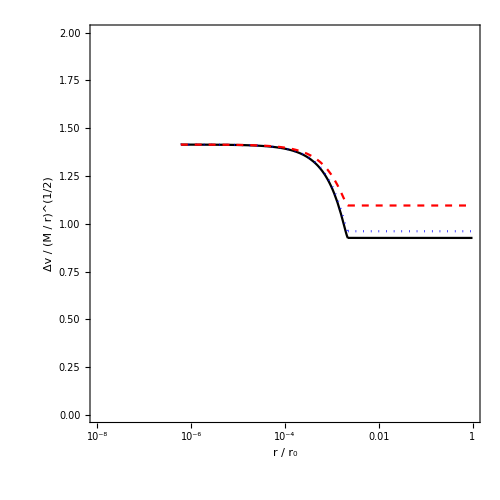

```mathematica
Show[LogLinearPlot[a1[r],{r,rann,1},PlotRange-> {{10^-8, 1},{0, 2}},PlotStyle->Black,FrameTicks-> {{Automatic,Automatic},{tPowerTicks[True][10^-8, 10^0],Automatic}}],LogLinearPlot[b1[r],{r,rbh,rann},PlotRange-> {{10^-8, 1},{0, 2}},PlotStyle->Black] ,LogLinearPlot[a2[r],{r,rann,1},PlotRange-> {{10^-8, 1},{0, 2}},PlotStyle->{Blue,Dotted}],LogLinearPlot[b2[r],{r,rbh,rann},PlotRange-> {{10^-8, 1},{0, 2}},PlotStyle->{Blue,Dotted}],LogLinearPlot[a3[r],{r,rann,1},PlotRange-> {{10^-8, 1},{0, 2}},PlotStyle->{Red,Dashed}],LogLinearPlot[b3[r],{r,rbh,rann},PlotRange-> {{10^-8, 1},{0,2}},PlotStyle->{Red,Dashed}]
 ,Frame-> True,AspectRatio-> 1,FrameLabel-> {"r / r_0","Δv / (M / r)^(1/2)"},LabelStyle-> Directive[Black,FontSize-> 25],FrameStyle-> Directive[Black,Thickness[0.0035]],ImageSize-> 500]
```

```mathematica
G=6.674 10^-20;(*Newton's constant in km^3/(kg s^2)*)
msol=1.989 10^30; (*solar mass in kg*)
M=6.5 10^9 msol; (*black hole mass NEED *)
clight=3 10^5;(* speed of light in km/s *)
v0=105;(*velocity dispersion km/s NEED*)
rh=(G M)/v0^2;
deg=42 (3.6 10^9)^-1(π/180); (* Shadow diameter angular extent in μas times conversion to rad *)
d=16.8 (3 10^19); (* distance to black hole in Mpc times conversion to km *)
rblackhole=d deg/2 ; (*"shadow" radius in km NEED*)
rboundary=0.2 rh; (*outer boundary*)
rstar=rblackhole/rboundary;
```

```mathematica
rs=(2G M)/clight^2 (* Schwarzchild radius *)
rblackhole/rs
```

1.91744×10^10

2.6761

```mathematica
luminosityout[r_,p_]:= r^3 densitycone[r,p]^2;
luminosityin[r_,p_]:=r^3 rhocone[r,p]^2;
```

```mathematica
u1[r_]=luminosityout[r,1];
v1[r_]=luminosityin[r,1];
```

```mathematica
u2[r_]=luminosityout[r,3/4];
v2[r_]=luminosityin[r,3/4];
```

```mathematica
u3[r_]=luminosityout[r,0];
v3[r_]=luminosityin[r,0];
```

```mathematica
t2PowerTicks[label_][min_,max_]:=Block[{min10,max10},min10=Floor[Log10[min]];
max10=Ceiling[Log10[max]];
Join[Table[{10^i,If[label,Superscript["10",i]]},{i,min10,max10,2}],Flatten[Table[{k 10^i,Spacer[{0,0}]},{i,min10,max10},{k,9}],1]]];
```

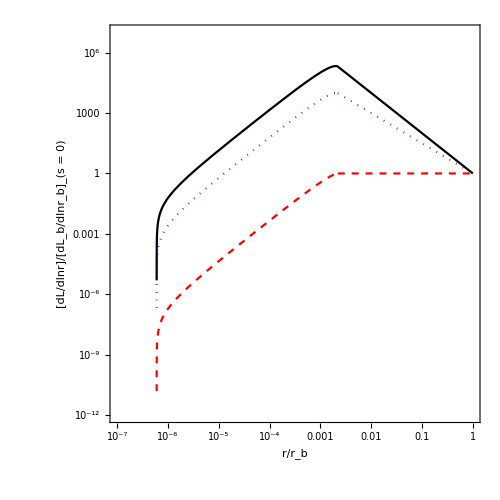

```mathematica
Show[LogLogPlot[u1[r],{r,rann,1},PlotRange->{{10^-7,1},{  10^-12,  10^7}},PlotStyle->Black, FrameTicks->{{t2PowerTicks[True][10^-12,10^7],Automatic},{tPowerTicks[True][10^-7,1],Automatic}}
],LogLogPlot[v1[r],{r,10^-8,rann},PlotStyle->Black],LogLogPlot[u2[r],{r,rann,1},PlotStyle->{Blue,Dotted}],LogLogPlot[v2[r],{r,10^-8,rann},PlotStyle->{Blue,Dotted}],LogLogPlot[u3[r],{r,rann,1},PlotStyle->{Red,Dashed}],LogLogPlot[v3[r],{r,10^-8,rann},PlotStyle->{Red,Dashed}],Frame-> True,AspectRatio-> 1,FrameLabel-> {"r/r_b","[dL/dlnr]/[dL_b/dlnr_b]_(s = 0)"},LabelStyle-> Directive[Black,FontSize-> 25],FrameStyle-> Directive[Black,Thickness[0.0035]],ImageSize-> 500]
```

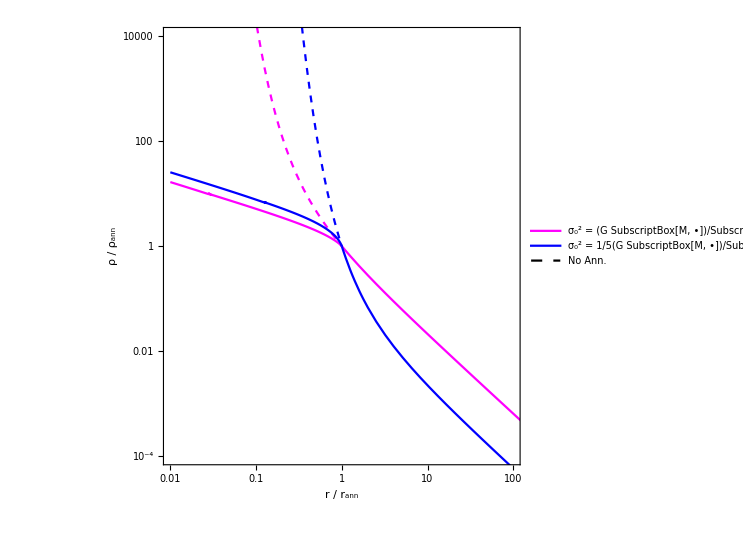

```mathematica
sidmDensity[x_,x0_]:=(ⅇ^(x0/x)(Erf[√(x0/x)]-Erf[√(x0/x-x0)])-2(√(x0/(π x))-ⅇ^x0 √(x0/(π x)-x0/π)))/(ⅇ^x0 Erf[√x0]-2 √(x0/π));       
sidmRho[x_,x0_]:=(ⅇ^(x0/x)Erf[√(x0/x)]-2 √(x0/(π x)))/(ⅇ^x0 Erf[√x0]-2 √(x0/π)); 
a=1/5; 
b=1;
c=5;
Show[LogLogPlot[sidmDensity[x,b],{x,10^-2,1},PlotStyle->{Magenta},PlotRange-> {{10^-2, 10^2},{10^-4, 10^4}},FrameTicks->{{tPowerTicks[True][10^-15,10^4],Automatic},{tPowerTicks[True][10^-4,10^5],Automatic}},PlotLegends-> Placed[LineLegend[{Magenta,Blue,{Black,Dashed}},{"σ_0^2 = (G SubscriptBox[M, •])/SubscriptBox[r, ann]","σ_0^2 = 1/5(G SubscriptBox[M, •])/SubscriptBox[r, ann]","No Ann."},LegendLayout->"Column",LabelStyle->Directive[Black,FontSize-> 17]],{0.8,0.85}]],
LogLogPlot[sidmRho[x,b],{x,1,10^5},PlotStyle->{Magenta}],
LogLogPlot[sidmRho[x,b],{x,10^-2,1},PlotStyle->{Magenta,Dashed}],LogLogPlot[sidmDensity[x,c],{x,10^-2,1},PlotStyle->{Blue}],
LogLogPlot[sidmRho[x,c],{x,1,10^5},PlotStyle->{Blue}],
LogLogPlot[sidmRho[x,c],{x,10^-2,1},PlotStyle->{Blue,Dashed}],Frame->True,AspectRatio->1,FrameLabel-> {"r / r_ann","ρ / ρ_ann"},LabelStyle-> Directive[Black,FontSize-> 25],FrameStyle-> Directive[Black,Thickness[0.0035]],ImageSize-> 550]
```

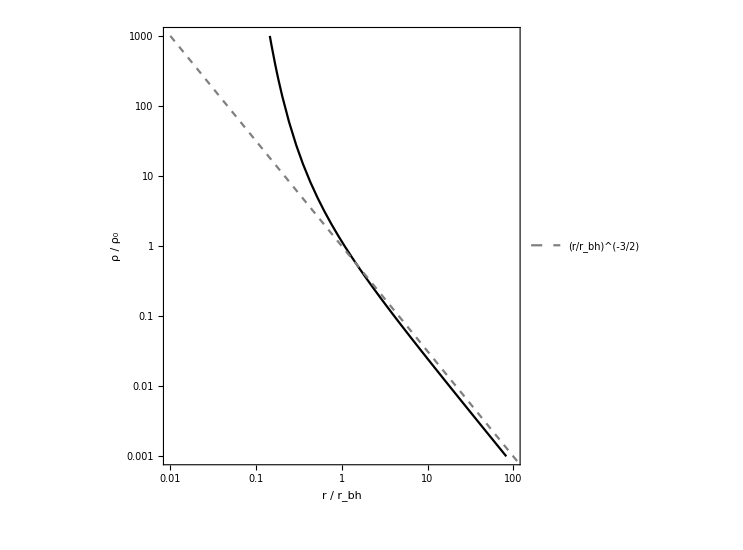

```mathematica
sidmRho2[x_,x0_]:=ⅇ^(x0/x)Erf[√(x0/x)]-2 √(x0/(π x));
line[x_,x0_]:=(x0/x)^(3/2);
Show[LogLogPlot[sidmRho2[x,10^0],{x,10^-2,10^2},PlotStyle->Black,PlotRange-> {{10^-2, 10^2},{10^-3, 10^3}},FrameTicks->{{tPowerTicks[True][10^-3,10^3],Automatic},{tPowerTicks[True][10^-2,10^2],Automatic}},PlotLegends-> Placed[LineLegend[{White,{Gray,Dashed}},{" ","(r/r_bh)^(-3/2)"},LegendLayout->"Column",LabelStyle->Directive[Black,FontSize-> 17]],{0.8,0.85}]],LogLogPlot[line[x,10^0],{x,10^-2,10^3},PlotStyle->{Gray,Dashed}],Frame->True,AspectRatio->1,FrameLabel-> {"r / r_bh","ρ / ρ_0"},LabelStyle-> Directive[Black,FontSize-> 25],FrameStyle-> Directive[Black,Thickness[0.0035]],ImageSize-> 550]
```

```mathematica
f
```

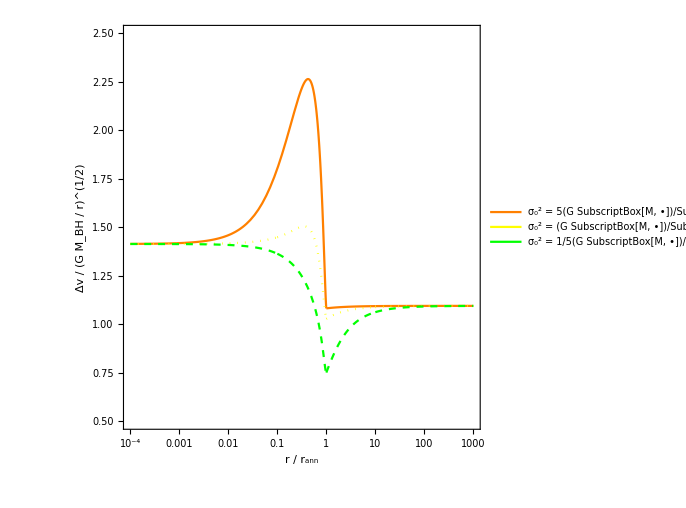

```mathematica
sidmVelocity[x_,x0_]:=√(x/x0)√((3 ⅇ^(x0/x)(Erf[√(x0/x)]-Erf[√(x0/x-x0)])-2/(√π)(√(x0/x)(3+2 x0/x)-√(x0/x-x0)(3+2(x0/x-x0))ⅇ^(x0/x)))/(ⅇ^(x0/x)(Erf[√(x0/x)]-Erf[√(x0/x-x0)])-2(√(x0/(π x))-√(x0/(π x)-x0/π)ⅇ^(x0/x))));       
sidmNu[x_,x0_]:=√(x/x0) √((3 ⅇ^(x0/x)Erf[√(x0/x)]-2/(√π)√(x0/x)(3+2 x0/x))/(ⅇ^(x0/x)Erf[√(x0/x)]-2 √(x0/(π x))));     
alpha=1/5; 
beta=1;
gamma=5;
Show[LogLinearPlot[sidmVelocity[x,alpha],{x, 10^-4,1},PlotStyle->Orange,PlotRange-> {{10^-4, 10^3},{0.5, 2.5}},PlotLegends-> Placed[LineLegend[{Orange,Yellow,Green},{"σ_0^2 = 5(G SubscriptBox[M, •])/SubscriptBox[r, ann]","σ_0^2 = (G SubscriptBox[M, •])/SubscriptBox[r, ann]","σ_0^2 = 1/5(G SubscriptBox[M, •])/SubscriptBox[r, ann]"},LegendLayout->"Column",LabelStyle->Directive[Black,FontSize-> 19]],{0.8,0.78}],FrameTicks->{{Automatic,Automatic},{tPowerTicks[True][10^-4,10^3],Automatic}}],LogLinearPlot[sidmNu[x,alpha],{x,1,10},PlotStyle->Orange],LogLinearPlot[sidmNu[x,alpha],{x,10,10^3},PlotStyle->Orange],LogLinearPlot[sidmVelocity[x,beta],{x, 10^-4,2 10^-1},PlotStyle->{Yellow,Dotted}],LogLinearPlot[sidmVelocity[x,beta],{x, 10^-1,10},PlotStyle->{Yellow,Dotted}],LogLinearPlot[sidmNu[x,beta],{x,1, 10},PlotStyle->{Yellow,Dotted}],LogLinearPlot[sidmNu[x,beta],{x,10, 10^3},PlotStyle->{Yellow,Dotted}],LogLinearPlot[sidmVelocity[x,gamma],{x, 10^-4,1.4 10^-1},PlotStyle->{Green,Dashed}],LogLinearPlot[sidmVelocity[x,gamma],{x, 10^-1,10},PlotStyle->{Green,Dashed}],LogLinearPlot[sidmNu[x,gamma],{x,1, 10},PlotStyle->{Green,Dashed}],LogLinearPlot[sidmNu[x,gamma],{x,10, 10^3},PlotStyle->{Green,Dashed}],Frame->True,AspectRatio->1,FrameLabel-> {"r / r_ann","Δv / (G M_BH / r)^(1/2)"},LabelStyle-> Directive[Black,FontSize-> 25],FrameStyle-> Directive[Black,Thickness[0.0035]],ImageSize-> 508]
```

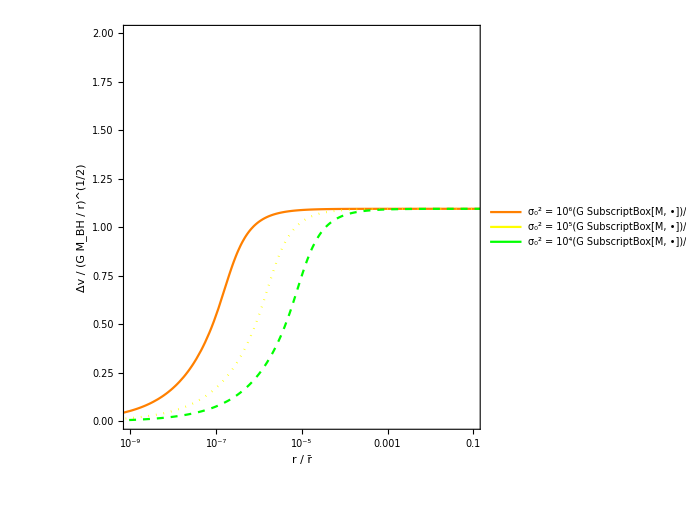

```mathematica
sidmNu2[x_,x0_]:=√(x/x0) √((3 ⅇ^(x0/x)Erf[√(x0/x)]-2/(√π)√(x0/x)(3+2 x0/x))/(ⅇ^(x0/x)Erf[√(x0/x)]-2 √(x0/(π x))));
Show[LogLinearPlot[sidmNu2[x,10^-6],{x, 10^-10,10^0},PlotStyle->Orange,PlotRange-> {{10^-9, 10^-1},{0, 2}},PlotLegends-> Placed[LineLegend[{Orange,Yellow,Green},{"σ_0^2 = 10^6(G SubscriptBox[M, •])/(r̄)","σ_0^2 = 10^5(G SubscriptBox[M, •])/(r̄)","σ_0^2 = 10^4(G SubscriptBox[M, •])/(r̄)"},LegendLayout->"Column",LabelStyle->Directive[Black,FontSize-> 17]],{0.8,0.78}],FrameTicks->{{Automatic,Automatic},{tPowerTicks[True][10^-10,10^0],Automatic}}],LogLinearPlot[sidmNu2[x,10^-5],{x, 10^-10,10^0},PlotStyle->{Yellow,Dotted}],LogLinearPlot[sidmNu2[x,5 10^-5],{x, 10^-10,10^0},PlotStyle->{Green,Dashed}],Frame->True,AspectRatio->1,FrameLabel-> {"r / r̄","Δv / (G M_BH / r)^(1/2)"},LabelStyle-> Directive[Black,FontSize-> 25],FrameStyle-> Directive[Black,Thickness[0.0035]],ImageSize-> 508]
```

```mathematica
rbh= 10^-7(*0*);
rann=2.2 10^-3;
starr[r_]:= 1/(1+rbh/r) ;  
starR[r_]:= 1/(1+rbh/rann)r/rann ;
```

```mathematica
sidmDensitycone[r_,r0_]:=1/r^(3/2)Integrate[ⅇ^(r0/r t)(√(1-t-rbh/r(1-rbh/r t))),{t,0,starr[r]}]/Integrate[ⅇ^(r0 t)(√(1-t-rbh(1-rbh t))),{t,0,starr[r]}];        
sidmRhocone[r_,r0_]:=1/r^(3/2)Integrate[ⅇ^(r0/r t)(√(1-t-rbh/r(1-rbh/r t))),{t,0,starR[r]},GenerateConditions->False]/Integrate[ⅇ^(r0 t)(√(1-t-rbh(1-rbh t))),{t,0,starr[r]}];
```

```mathematica
f1[r_]=sidmDensitycone[r,5 10^-7];    
g1[r_]=sidmRhocone[r,5 10^-7];
```

```mathematica
f2[r_]=sidmDensitycone[r,10^-6];
g2[r_]=sidmRhocone[r,10^-6];
```

```mathematica
f3[r_]=sidmDensitycone[r, 10^-5];
g3[r_]=sidmRhocone[r, 10^-5];
```

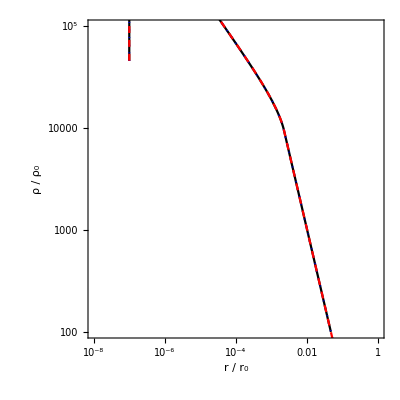

```mathematica
Show[LogLogPlot[f1[r],{r,rann,1},PlotRange->{{10^-8,1},{100, 10^5}},PlotStyle->Black],LogLogPlot[g1[r],{r,10^-8,rann},PlotStyle->Black],LogLogPlot[f2[r],{r,rann,1},PlotStyle->{Blue,Dotted}],LogLogPlot[g2[r],{r,10^-8,rann},PlotStyle->{Blue,Dotted}],LogLogPlot[f3[r],{r,rann,1},PlotStyle->{Red,Dashed}],LogLogPlot[g3[r],{r,10^-8,rann},PlotStyle->{Red,Dashed}],AspectRatio-> 1,FrameLabel-> {"r / r_0","ρ / ρ_0"},Frame-> True]
```

```mathematica
sidmVelocitycone[r_,r0_]:=√2 √(Integrate[ⅇ^(r0/r t)(1-t)√(1-t-rbh/r(1-rbh/r t)),{t,0,starr[r]}]/Integrate[ⅇ^(r0/r t)√(1-t-rbh/r(1-rbh/r t)),{t,0,starr[r]}]);   
sidmNucone[r_,r0_]:=√2 √(Integrate[ⅇ^(r0/r t)(1-t)√(1-t-rbh/r(1-rbh/r t)),{t,0,starR[r]}]/Integrate[ⅇ^(r0/r t)√(1-t-rbh/r(1-rbh/r t)),{t,0,starR[r]}]);
```

```mathematica
m1[r_]=sidmVelocitycone[r,5 10^-7];  
n1[r_]=sidmNucone[r,5 10^-7];
```

```mathematica
m2[r_]=sidmVelocitycone[r,10^-6];
n2[r_]=sidmNucone[r,10^-6];
```

```mathematica
m3[r_]=sidmVelocitycone[r, 10^-5];
n3[r_]=sidmNucone[r,10^-5];
```

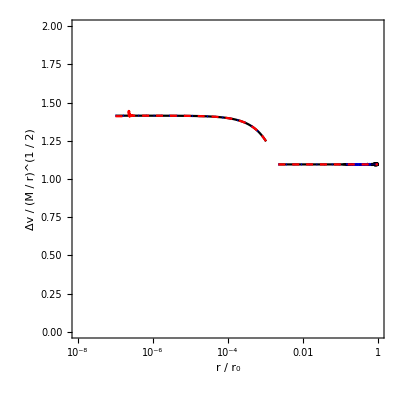

```mathematica
Show[LogLinearPlot[m1[r],{r,rann,1},PlotRange-> {{10^-8, 1},{0, 2}},PlotStyle->Black],LogLinearPlot[n1[r],{r,rbh,rann},PlotStyle->Black] ,LogLinearPlot[m2[r],{r,rann,1},PlotStyle->{Blue,Dotted}],LogLinearPlot[n2[r],{r,rbh,rann},PlotStyle->{Blue,Dotted}],LogLinearPlot[m3[r],{r,rann,1},PlotStyle->{Red,Dashed}],LogLinearPlot[n3[r],{r,rbh,rann},PlotStyle->{Red,Dashed}]
 ,Frame-> True,AspectRatio-> 1,FrameLabel-> {"r / r_0","Δv / (M / r)^(1 / 2)"}]
```

```mathematica
rblh=5 10^15(* cm *)
```

5000000000000000

```mathematica
ra=2rblh;
fin[r_,p_]:=(ra/r)^(3/2+p)Integrate[t^p(√(1-t-rblh/r(1-rblh/r t))),{t,0,1/(1+rblh/ra)r/ra},GenerateConditions->False]/Integrate[t^p(√(1-t-rblh/ra(1-rblh/ra t))),{t,0,1/(1+rblh/ra)}];
```

```mathematica
Msgr=4 10^6 msol; (*black hole mass NEED *)
rsgr=4(G Msgr)/c^2 (* Black hole radius for sgrA* *)
degree=1 (π/180);
dist=8.5  (3 10^16); (* distance to GC in Kpc times conversion to km *)
rdis=dist degree/2 (*"shadow" radius in km NEED*)
Rh=1.7 (3 10^13); (* parsec times conversion to km *)
rb=0.2 Rh
4π(-(rsgr 10^5)^3+(rdis 10^5)^3)
```

8.49574×10^16

2.22529×10^15

1.02×10^13

-7.70557×10^66

NDSolve::ndsz: At r == 0.999999999999999999999999999999999999999999999999999999904325, step size is effectively zero; singularity or stiff system suspected.

{{f→InterpolatingFunction[…]}}

NDSolve::ndsz: At r == 0.999999999999999999999999999999999999999999999999999999822203, step size is effectively zero; singularity or stiff system suspected.

{{f→InterpolatingFunction[…]}}

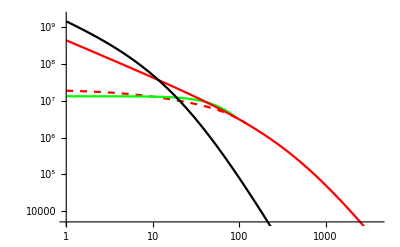

```mathematica
G=7 10^-20(1/(3 10^16))^3((2 10^30)/1);(*Newton's constant in kpc^3/(msol s^2)*)
v0=900(1/(3 10^16)); (* kpc/s *)
rhos=   9 10^5; (*scale density msol/kpc^3 *)
rs=500; (* scale radius kpc *)
nfw[r_]=rhos/(r/rs(1+r/rs)^2); 
r0=20;(*kpc*)
rhoB0=((1000(1/(3 10^16)))^2)/(2π G r0^2);(*msol/kpc^3*)
rhoB[r_]=rhoB0/(r/r0(1+r/r0)^3);
rho0= 20 10^6;(*msol/kpc^3*)
a0=(4π G r0^2)/v0^2 rho0;
a1=((1000 (1/(3 10^16)))/v0)^2;
sol=NDSolve[{f''[r]+2/r f'[r]+a0/(1-r)^4 ⅇ^f[r]+(2 a1)/r==0,f[10^-10]==0,f'[10^-10]==-a1 },f,{r,10^-10,4000},PrecisionGoal->20,AccuracyGoal->20,WorkingPrecision->60,MaxSteps->5000,Method->"StiffnessSwitching"]
sol2=NDSolve[{f''[r]+2/r f'[r]+a0/(1-r)^4 ⅇ^f[r]==0,f[10^-10]==0,f'[10^-10]==-a0/10 10^-10/3 },f,{r,10^-10,4000},PrecisionGoal->20,AccuracyGoal->20,WorkingPrecision->60,MaxSteps->5000,Method->"StiffnessSwitching"]
r1=120;(*kpc*)
Show[LogLogPlot[rho0 ⅇ^f[(r/r0)/(1+r/r0)]/.sol,{r,10^0,r1},PlotRange->{{10^0,4000},{5 10^3,2 10^9}},PlotStyle->{Red,Dashed}],LogLogPlot[rho0/1.5 ⅇ^f[(r/r0)/(1+r/r0)]/.sol2,{r,10^0,r1},PlotStyle->{Green}],
LogLogPlot[nfw[r],{r,10^0,4000},PlotStyle->Red],LogLogPlot[rhoB[r],{r,10^0,4000},PlotStyle->Black]]
```

NDSolve::ndsz: At r == 0.999999999999999999999999999999999999999999999999999977424805, step size is effectively zero; singularity or stiff system suspected.

{{f→InterpolatingFunction[…]}}

NDSolve::ndsz: At r == 0.999999999999999999999999999999999999999999999999999999142164, step size is effectively zero; singularity or stiff system suspected.

{{f→InterpolatingFunction[…]}}

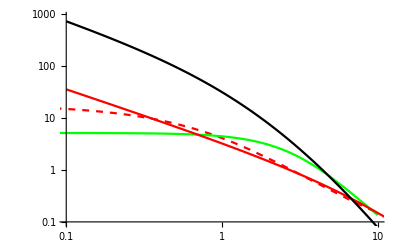

```mathematica
G=7 10^-8(1/(6 10^23));(*Newton's constant in cm^3/(GeV s^2)*)
v0=160 10^5; (* cm/s *)
r0=27/10;(*kpc*)
rhoB0=30;(*GeV/cm^3*)
rhoB[r_]=rhoB0/(r/r0(1+r/r0)^3);
r1=10; (*thermalized region in kpc*)
rhos=   0.2; (*scale density Gev/cm^3 *)
rs=18; (* scale radius kpc *)
nfw[r_]=rhos/(r/rs(1+r/rs)^2); 
rho0=18;(*GeV/cm^3*)
a0=(4π G (r0 3 10^21)^2)/v0^2 rho0;
a1=((365 10^5)/v0)^2;
sol=NDSolve[{f''[r]+2/r f'[r]+a0/(1-r)^4 ⅇ^f[r]+(2 a1)/r==0,f[10^-10]==0,f'[10^-10]==-a1 },f,{r,10^-10,r1},PrecisionGoal->20,AccuracyGoal->20,WorkingPrecision->60,MaxSteps->5000,Method->"StiffnessSwitching"]
sol2=NDSolve[{f''[r]+2/r f'[r]+a0/(1-r)^4 ⅇ^f[r]==0,f[10^-10]==0,f'[10^-10]==- (10 a0)/35 10^-10/3 },f,{r,10^-10,r1},PrecisionGoal->20,AccuracyGoal->20,WorkingPrecision->60,MaxSteps->5000,Method->"StiffnessSwitching"]
Show[LogLogPlot[rho0 ⅇ^f[(r/r0)/(1+r/r0)]/.sol,{r,10^-9,r1},PlotRange->{{10^-1,10},{10^-1,9 10^2}},PlotStyle->{Red,Dashed}],LogLogPlot[rho0/3.5 ⅇ^f[(r/r0)/(1+r/r0)]/.sol2,{r,10^-9,r1},PlotRange->{{10^-1,10},{10^-1,9 10^2}},PlotStyle->Green],LogLogPlot[nfw[r],{r,10^-1,10^3},PlotStyle->Red],LogLogPlot[rhoB[r],{r,0.1,10},PlotStyle->Black]]
```

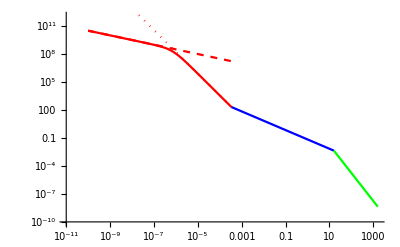

```mathematica
rh=1.7 10^-3; (* kpc *)
rb=0.2 rh; (* kpc *)
rhoD=0.008; (* msol/pc^3 *)
Dis=8.5; (* kpc *)
rhob=rhoD(Dis/rb)^1; (* msol/pc^3 *)
rhoann=1.7 10^8 ; (* msol/pc^3 *)
rin=3.1 10^-6; (* kpc *)
rH=16; (* kpc *)
rhoH=rhoD(Dis/rH)^1; (* msol/pc^3 *)
aa[x_]:=(rhob(rb/x)^(7/3)rhoann(rin/x)^(1/2))/(rhob(rb/x)^(7/3)+rhoann(rin/x)^(1/2));
f[x_]:=rhob(rb/x)^(7/3);
g[x_]:=rhoann(rin/x)^(1/2);
bb[x_]:=rhob(rb/x)^1;
cc[x_]:=rhoH(rH/x)^3
Show[LogLogPlot[aa[x],{x,10^-10,rb},PlotRange->{{ 10^-11,100rH},{10^-10,10^12}},PlotStyle->Red],LogLogPlot[f[x],{x,10^-10,rb},PlotStyle->{Red,Dotted}],LogLogPlot[g[x],{x,10^-10,rb},PlotStyle->{Red,Dashed}],LogLogPlot[bb[x],{x,rb,rH},PlotStyle->Blue],LogLogPlot[cc[x],{x,rH,100rH},PlotStyle->Green]]
```

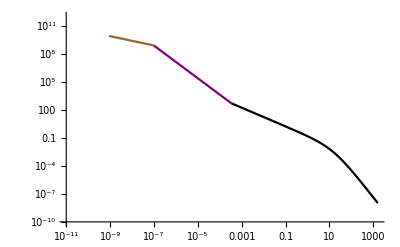

```mathematica
rin2= 10^-1.5 rin; (* kpc *)
GNew=7 10^-20(1/(3 10^16))^3((2 10^30)/1);(*Newton's constant in kpc^3/(msol s^2)*)
light=9.7 10^-12;(* speed of light in kpc/s *)
M=4 10^6;(* msol *)
rsh=(4GNew M)/light^2;(* kpc *)
rhoann2=rhob(rb/rin2)^(7/4);(* msol/pc^3 *)
aA[x_]:=2.5rhoann2(rin2/x)^(1/2);
bB[x_]:=2.5rhob(rb/x)^(7/4);
cC[x_]:=(2.5rhoH)/(x/rH(1+x/rH)^2);
Show[LogLogPlot[aA[x],{x,rsh,rin2},PlotRange->{{ 10^-11,100rH},{10^-10,10^12}},PlotStyle->Brown],LogLogPlot[bB[x],{x,rin2,rb},PlotStyle->Purple],LogLogPlot[cC[x],{x,rb,100rH},PlotStyle->Black],LogLogPlot[b[x],{x,rb,rH},PlotStyle->{Blue,Dotted}],LogLogPlot[c[x],{x,rH,100rH},PlotStyle->{Green,Dotted}],LogLogPlot[a[x],{x,rsh,rb},PlotStyle->{Red,Dotted}]]
```

```mathematica
(****************************)
(***** Density Profiles *****)
(****************************)
BHCDMa[r_]:=Piecewise[{{0,r<rsh},{aa[r], rsh≤ r< rb},{bb[r],rb≤ r<rH},{cc[r],r≥ rH}}];
BHCDMb[r_]:=Piecewise[{{0,r<rsh},{aA[r],rsh≤ r<rin2},{bB[r],rin2≤ r<rb},{cC[r],r≥ rb}}];
CDMa[r_]:=Piecewise[{{bb[r],0≤ r<rH},{cc[r],r≥ rH}}];
CDMb[r_]:=cC[r];
```

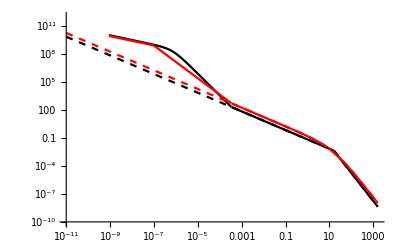

```mathematica
Show[LogLogPlot[BHCDMa[r],{r,10^-11,100 rH},PlotRange->{{ 10^-11,100rH},{10^-10,10^12}},PlotStyle->Black],LogLogPlot[BHCDMb[r],{r,10^-11,100 rH},PlotStyle->Red],LogLogPlot[CDMa[r],{r,10^-11,100 rH},PlotStyle->{Black,Dashed}],LogLogPlot[CDMb[r],{r,10^-11,100 rH},PlotStyle->{Red,Dashed}]]
```

```mathematica
(***************************)
(****** MW Model Data ******)
(******  Msol / kpc^3 ******)
(***************************)
```

```mathematica
rhodata={{1.1564146847382017,293172004.43277615},
{1.21026517132478,262249435.16902325},
{1.2666925939437252,244180573.05355084},
{1.3257508896133527,229079653.11577427},
{1.3876453774363149,214831310.22343695},
{1.4522564665615185,201430133.04060605},
{1.519966495182818,187410146.69324327},
{1.590833437256707,173849923.963236},
{1.6638729025549805,161533314.87617737},
{1.744025670657765,147717861.9884481},
{1.8239516060257375,141029848.13314354},
{1.9089189718228787,130468275.31446522},
{1.9942344493118385,122460174.04894993},
{2.091071514785291,114078004.12020302},
{2.1885656663868533,106200264.36136034},
{2.2906053868650886,98229975.01612973},
{2.3936681724272577,91340331.05562449},
{2.5091791463067707,83787938.37610878},
{2.626167154777934,77766695.26032509},
{2.7486096140188607,72093438.18870386},
{2.8741915235203352,67291960.49850762},
{3.0129483374393695,61182599.18089797},
{3.154198643342215,57689887.89108086},
{3.30409062315285,52406128.10785594},
{3.4535088004175236,48488488.58637133},
{3.6193729992354937,43864203.59229758},
{3.788122703583264,40424994.87411818},
{3.9647401968335547,37134792.5860492},
{4.144265818597883,34374443.294830576},
{4.343062964692523,31228372.93981622},
{4.545554001513105,28816929.423955664},
{4.757485983658684,26382834.936382476},
{4.97557773839102,24216477.547619566},
{5.211454005781664,21982150.363415606},
{5.455115276907145,19950021.469190903},
{5.708842506585785,18645509.043934286},
{5.971092736496757,16923086.414401624},
{6.253478956020743,15438579.301270854},
{6.545041258440638,14151921.903266719},
{6.850197366291116,12946765.880293677},
{7.165790656377912,11845570.709687285},
{7.503855739685985,10808669.252304755},
{7.85371562917729,9882414.74389918},
{8.215825385299398,9054338.152713599},
{8.511379000736193,8615187.160362925},
{9.048603336117186,7534664.5340194},
{9.49484541262771,6860083.238249265},
{9.936378071290196,6409848.732766917},
{10.405722162585105,5831858.768379207},
{10.891871750335687,5350581.306906461},
{11.399694552255033,4909326.902809953},
{11.93119409257715,4506351.818671334},
{12.48607962042937,4147558.659471541},
{13.069690475409832,3814158.155823975},
{13.679051932244528,3509213.4593742057},
{14.31682426734557,3229461.9416468036},
{14.981483684695132,2978935.3995764693},
{15.682961848844199,2747810.8379203086},
{16.414164511805122,2535413.1939790966},
{17.198412114848537,2305705.4504420166},
{17.980434139045272,2181451.035737925},
{18.81875418664727,1989466.2979816333},
{19.69616008149726,1834454.9293047255},
{20.61447416275971,1691616.035954056},
{21.568375569589207,1557199.932493512},
{22.581545026429673,1427898.8201272006},
{23.63438734130875,1310325.3356662495},
{24.73631739304119,1202399.2537793182},
{25.882395789732357,1105143.8486405518},
{27.096702083631325,1015318.2917724184},
{28.36005915304039,933672.8037956699},
{29.65186268425673,854042.225744655},
{31.054571557675263,793872.8128175404},
{32.514660221420556,722616.2702018556},
{34.03062425731626,661652.6693560199},
{35.61726862456029,605883.0931403766},
{37.274490030467376,554927.9145995426},
{39.01593360149417,506347.9921965385},
{40.83501311098245,461947.59935385885},
{42.73890541248635,421617.37086888816},
{44.735643449746185,384482.4221210854},
{46.81713000935352,349517.6875370241},
{48.99993262438054,317215.2149419118},
{51.28450626328749,287713.04318088136},
{53.6941960397838,258725.29321877533},
{56.17816773782828,239529.53900605955},
{58.79741952496387,214510.36773339877},
{61.53879134912937,194788.75123187128},
{64.42984969570955,175690.74573676998},
{67.41093547915135,159361.2035802044},
{69.05701170101712,151039.5015377943}};
rhofunc=Interpolation[rhodata]
```

InterpolatingFunction[…]

```mathematica
b0=(Log[1.16]Log[rhofunc[1.5]]-Log[1.5]Log[rhofunc[1.16]])/(Log[1.16]-Log[1.5]);
ms=(Log[rhofunc[1.16]]-b0)/Log[1.16];
extrap[x_]:=ⅇ^b0 x^ms
```

```mathematica
rhofunc[1.16]
extrap[1.16]
```

2.905×10^8

2.905×10^8

```mathematica
dense=rhofunc[69] 69/rH(1+69/rH)^2;
nfw[x_]=dense/(x/rH(1+x/rH)^2);
```

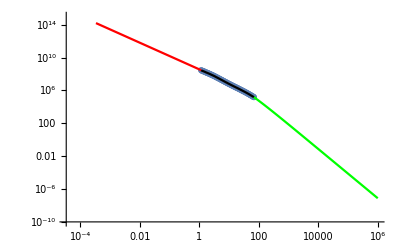

```mathematica
Show[ListLogLogPlot[rhodata,PlotRange->{{rb/10,10^6},{10^-10,10^15}}],LogLogPlot[rhofunc[r],{r,1.16,70},PlotStyle->Black],LogLogPlot[extrap[r],{r,rb,1.16},PlotStyle->Red],LogLogPlot[nfw[r],{r,69,10^6},PlotStyle->Green]]
```

```mathematica
ran= .00005rb;
ran2= .00005rb;
```

```mathematica
B1[x_]:=extrap[rb](rb/x)^(3/2);
C1[x_]:=rhofunc[1.16];
B2[x_]:=C1[x](rb/x)^(3/2);
A1[x_]:=B1[ran](ran/x)^(1/2); 
A2[x_]:=B2[ran2](ran2/x)^(1/2);
A3[x_]:=extrap[ran](ran/x)^(1/2);
```

```mathematica
test1[r_]:=Piecewise[{{0,r<rsh},{A1[r],rsh≤ r<ran},{B1[r], ran≤ r< rb},{extrap[r],rb≤ r<1.16},{rhofunc[r],1.16≤ r<69},{nfw[r],69≤ r}}];
test3[r_]:=Piecewise[{{0,r<rsh},{A2[r],rsh≤ r<ran2},{B2[r], ran2≤ r< rb},{C1[r],rb≤ r<1.16},{rhofunc[r],1.16≤ r<69},{nfw[r],69≤ r}}];
test4[r_]:=Piecewise[{{C1[r], r<1.16},{rhofunc[r],1.16≤ r<69},{nfw[r],69≤ r}}];
test5[r_]:=Piecewise[{{A3[r],0≤ r<ran},{extrap[r],ran≤ r<1.16},{rhofunc[r],1.16≤ r<69},{nfw[r],69≤ r}}];
```

```mathematica
(*****************************)
(*** Density Interpolation ***)
(*****************************)
j=1000;
SIDMBH=Interpolation[Table[{10^6 10^(-(50(j-i))/j),test1[10^6 10^(-(50(j-i))/j)]},{i,0,j}]];
SIDM=Interpolation[Table[{10^6 10^(-(50(j-i))/j),test5[10^6 10^(-(50(j-i))/j)]},{i,0,j}]];
SIDMBHCore=Interpolation[Table[{10^6 10^(-(50(j-i))/j),test3[10^6 10^(-(50(j-i))/j)]},{i,0,j}]];
SIDMCore=Interpolation[Table[{10^6 10^(-(50(j-i))/j),test4[10^6 10^(-(50(j-i))/j)]},{i,0,j}]];
```

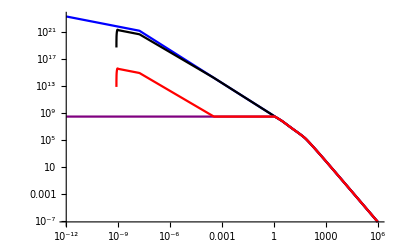

```mathematica
Show[LogLogPlot[SIDM[r],{r,10^-12,10^6},PlotStyle->Blue],LogLogPlot[SIDMBH[r],{r,rsh/10,10^6},PlotRange->{{10^-12,10^6},{10^-10,10^30}},PlotStyle->Black],LogLogPlot[SIDMCore[r],{r,10^-12,10^6},PlotStyle->Purple],LogLogPlot[SIDMBHCore[r],{r,10^-12,10^6},PlotStyle->Red]]
```

```mathematica
(*****************************)
(********* J-Factor **********)
(******** Calculator *********)
(*****************************)
Dis=8.5; (* Distance from Earth to Galactic Center kpc *)
r[θ_,s_]:=√(Dis^2+s^2-2Dis s Cos[θ]);
ρBHCDMa[θ_,s_]=BHCDMa[r[θ,s]];  
ρBHCDMb[θ_,s_]=BHCDMb[r[θ,s]];  
ρCDMa[θ_,s_]=CDMa[r[θ,s]];  
ρCDMb[θ_,s_]=CDMb[r[θ,s]];  
ρSIDMBH[θ_,s_]=SIDMBH[r[θ,s]];   
ρSIDMBHCore[θ_,s_]=SIDMBHCore[r[θ,s]];  
ρSIDM[θ_,s_]=SIDM[r[θ,s]];   
ρSIDMCore[θ_,s_]=SIDMCore[r[θ,s]];  
smax=∞; (* kpc *)
θmax=π/180(1); (* rad *)
Off[NIntegrate::inumr]
funcBHCDMa[θ_]=NIntegrate[ρBHCDMa[θ,s]^2/(8.33 BHCDMa[8.33]^2),{s,0,smax}]; 
funcBHCDMb[θ_]=NIntegrate[ρBHCDMb[θ,s]^2/(8.33 BHCDMb[8.33]^2),{s,0,smax}]; 
funcCDMa[θ_]=NIntegrate[ρCDMa[θ,s]^2/(8.33 CDMa[8.33]^2),{s,0,smax}];
funcCDMb[θ_]=NIntegrate[ρCDMb[θ,s]^2/(8.33 CDMb[8.33]^2),{s,0,smax}];
funcSIDMBH[θ_]=NIntegrate[ρSIDMBH[θ,s]^2/(8.33 SIDMBH[8.33]^2),{s,0,smax}];
funcSIDMBHCore[θ_]=NIntegrate[ρSIDMBHCore[θ,s]^2/(8.33 SIDMBHCore[8.33]^2),{s,0,smax}];
funcSIDM[θ_]=NIntegrate[ρSIDM[θ,s]^2/(8.33 SIDM[8.33]^2),{s,0,smax}];
funcSIDMCore[θ_]=NIntegrate[ρSIDMCore[θ,s]^2/(8.33 SIDMCore[8.33]^2),{s,0,smax}];
```

```mathematica
plot1=LogPlot[funcBHCDMa[π/180 x],{x,0,180 },PlotStyle->{Blue},PlotRange->{{0,180},{10^-1,10^3}}];
```

```mathematica
plot2=LogPlot[funcBHCDMb[π/180 x],{x,0,180 },PlotStyle-> {Red},PlotRange->{{0,180},{10^-1,10^3}}];
```

```mathematica
plot3=LogPlot[funcCDMa[π/180 x],{x,0,180 },PlotStyle-> {Green,Dotted},PlotRange->{{0,180},{10^-1,10^3}}];
```

```mathematica
plot4=LogPlot[funcCDMb[π/180 x],{x,0,180 },PlotStyle->{ Yellow,Dotted},PlotRange->{{0,180},{10^-1,10^3}},PlotLegends-> Placed[LineLegend[{Blue,Red,Gray,Black,Yellow,Green},{"BHCDMa","BHCDMb","SIDMa","SIDMb","CDMa","CDMb"},LegendLayout->"Column"],{0.8,0.8}]];
```

```mathematica
plot5=LogPlot[funcSIDMBH[π/180 x],{x,0,180 },PlotStyle-> {Black,Dotted},PlotRange->{{0,180},{10^-1,10^3}},PlotLegends-> Placed[LineLegend[{Black,Gray,Blue,Purple},{"SIDMBH","SIDMBHCore","SIDM","SIDMCore"},LegendLayout->"Column"],{0.8,0.8}]];
```

```mathematica
plot6=LogPlot[funcSIDMBHCore[π/180 x],{x,0,180 },PlotStyle-> {Gray,Dashed},PlotRange->{{0,180},{10^-1,10^3}}];
```

```mathematica
plot6a=LogPlot[funcSIDMCore[π/180 x],{x,0,180 },PlotStyle-> {Purple,DotDashed},PlotRange->{{0,180},{10^-1,10^3}}];
```

```mathematica
plot5a=LogPlot[funcSIDM[π/180 x],{x,0,180 },PlotStyle-> {Blue},PlotRange->{{0,180},{10^-1,10^3}}];
```

```mathematica
plot7=LogPlot[funcSIDMBH[π/180 x],{x,0,2 },PlotStyle-> {Black,Dotted},PlotRange->{{0,2},{10^1,10^15}}];
```

```mathematica
plot8=LogPlot[funcSIDMBHCore[π/180 x],{x,0,2 },PlotStyle-> {Gray,Dashed},PlotRange->{{0,2},{10^1,10^15}}];
```

```mathematica
plot8a=LogPlot[funcSIDMCore[π/180 x],{x,0,2 },PlotStyle-> {Purple,DotDashed},PlotRange->{{0,2},{10^1,10^15}}];
```

```mathematica
plot7a=LogPlot[funcSIDM[π/180 x],{x,0,2 },PlotStyle-> {Blue},PlotRange->{{0,2},{10^1,10^15}}];
```

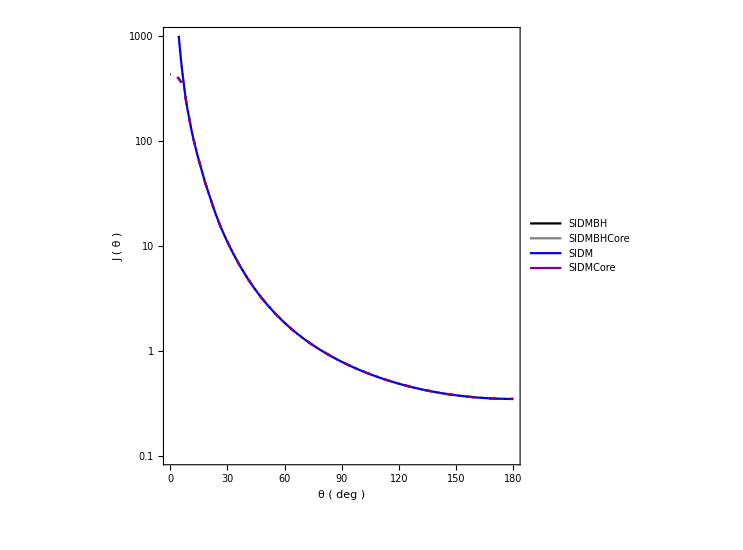

```mathematica
Show[plot5a,plot6a,plot5,plot6a,ImageSize-> 550,Frame-> True,FrameStyle-> Directive[Thickness[0.002],Black,FontSize-> 20],FrameLabel-> {"θ ( deg )","J ( θ )"},LabelStyle->Directive[Black,FontSize-> 18],AspectRatio-> 1]
```

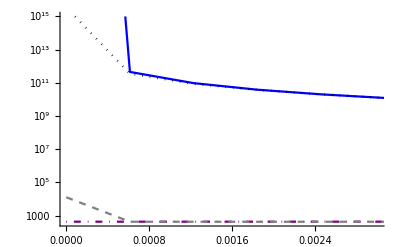

```mathematica
Show[plot7a,plot8a,plot7,plot8,PlotRange-> {{0,0.003},All}]
```

```mathematica
JBHCDMa=2π NIntegrate[Sin[θ]funcBHCDMa[θ],{θ,0,θmax}] ;
```

```mathematica
JBHCDMb=2π NIntegrate[Sin[θ]funcBHCDMb[θ],{θ,0,θmax}] ;
```

```mathematica
JCDMa=2π NIntegrate[Sin[θ]funcCDMa[θ],{θ,0,θmax}] ;
```

```mathematica
JCDMb=2π NIntegrate[Sin[θ]funcCDMb[θ],{θ,0,θmax}] ;
```

```mathematica
JSIDMBH=2π NIntegrate[Sin[θ]funcSIDMBH[θ],{θ,0,θmax}] ;
```

```mathematica
JSIDM=2π NIntegrate[Sin[θ]funcSIDM[θ],{θ,0,θmax}] ;
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {2.59887×10^-8}. NIntegrate obtained 1.33111×10^41 and 1.73247×10^40 for the integral and error estimates.

```mathematica
JSIDMBHCore=2π NIntegrate[Sin[θ]funcSIDMBHCore[θ],{θ,0,θmax}] ;
```

```mathematica
JSIDMCore=2π NIntegrate[Sin[θ]funcSIDMCore[θ],{θ,0,θmax}] ;
```

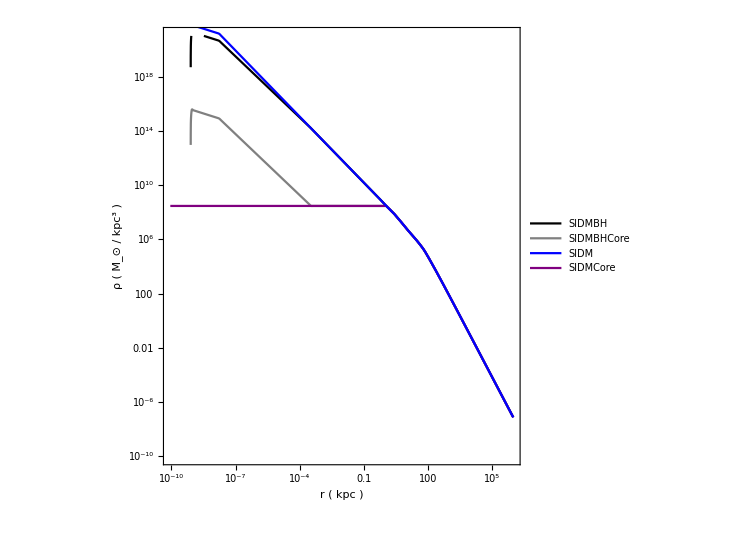

```mathematica
Show[LogLogPlot[SIDMBH[r],{r,rsh/10,10^6},PlotStyle->Black,PlotRange->{{rsh/10,10^6},{10^-10,10^21}},PlotLegends-> Placed[LineLegend[{Black,Gray,Blue,Purple},{"SIDMBH","SIDMBHCore","SIDM","SIDMCore"},LegendLayout->"Column",LabelStyle->Directive[FontSize-> 15]],{0.8,0.8}]],LogLogPlot[SIDMBHCore[r],{r,rsh/10,10^6},PlotStyle->Gray],LogLogPlot[SIDMCore[r],{r,rsh/10,10^6},PlotStyle->Purple],LogLogPlot[SIDM[r],{r,rsh/10,10^6},PlotStyle->Blue],ImageSize-> 550,Frame-> True,FrameStyle-> Directive[Thickness[0.002],Black,FontSize-> 20],FrameLabel-> {"r ( kpc )","ρ ( M_⊙ / kpc^3 )"},LabelStyle->Directive[Black,FontSize-> 18],AspectRatio-> 1]
```

```mathematica
SIDMBH[8.33]
```

8.82689×10^6

```mathematica
SIDMBHCore[8.33]
```

8.82689×10^6

```mathematica
SIDM[8.33]
```

8.82689×10^6

```mathematica
SIDMCore[8.33]
```

8.82689×10^6

```mathematica
10^9 CDMa[8.33]
```

8.16327×10^6

```mathematica
10^9 CDMb[8.33]
```

8.82591×10^6

```mathematica
10^9 BHCDMa[8.33]
```

8.16327×10^6

```mathematica
10^9 BHCDMb[8.33]
```

8.82591×10^6

```mathematica
4π NIntegrate[r^2 SIDMBH[r],{r,0,60}]
```

5.33177×10^11

```mathematica
4π NIntegrate[r^2 SIDMBHCore[r],{r,0,60}]
```

5.30943×10^11

```mathematica
4π NIntegrate[r^2 SIDM[r],{r,0,60}]
```

5.33177×10^11

```mathematica
4π NIntegrate[r^2 SIDMCore[r],{r,0,60}]
```

5.30943×10^11

```mathematica
4π NIntegrate[r^2 10^9 CDMa[r],{r,0,60}]
```

3.98519×10^11

```mathematica
4π NIntegrate[r^2 10^9 CDMb[r],{r,0,60}]
```

4.20377×10^11

```mathematica
4π NIntegrate[r^2 10^9 BHCDMa[r],{r,0,60}]
```

3.98519×10^11

```mathematica
4π NIntegrate[r^2 10^9 BHCDMb[r],{r,0,60}]
```

4.20377×10^11

```mathematica
JBHCDMa
```

8.59664

```mathematica
JBHCDMb
```

2.19336

```mathematica
JCDMa
```

0.341556

```mathematica
JCDMb
```

1.698

```mathematica
JSIDMBH
```

2301.95

```mathematica
JSIDMBHCore
```

0.407313

```mathematica
JSIDM
```

8.36359×10^41

```mathematica
JSIDMCore
```

0.41174

```mathematica
(***************************)
(** P-Wave Xsection Limit **)
(***************************)
```

```mathematica
Φ=7.74 10^-8;(* Excess gamma flux (1-100 Gev range) cm^-2 s^-1 *)
r0=8.5(3.086 10^21) ;(* Distance from galactic center to solar neighborhood cm  *)
rho0=0.008 (10^3)^3(3.086 10^21)^-3(1.8 10^-27)^-1(2 10^30);(* DM density in the solar neighborhood GeV cm^-3 *)
Jfactor=JSIDM;
ξfactor=31.3397;
dm=100;(* DM mass in GeV*)
(dm^2 8 π Φ)/(Jfactor ξfactor r0 rho0^2)(* cross section limit cm^3 s^-1 *)
```

3.09285×10^-67

```mathematica
(***********************)
(**** Mass Function ****)
(******** Msol *********)
(***********************)
```

```mathematica
l=250;
mass[r_]:=4 π NIntegrate[x^2 SIDMBH[x],{x,0,r}];
massSIDMBH=Table[{10^6 10^(-(17(l-i))/l),mass[10^6 10^(-(17(l-i))/l)]},{i,0,l}];
```

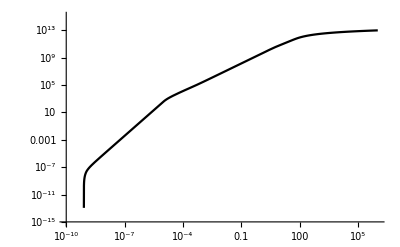

```mathematica
Mass=Interpolation[massSIDMBH];
LogLogPlot[Mass[r],{r,7 10^-10,10^6},PlotRange->{{10^-10,10^6},{10^-15,10^15}},PlotStyle->Black]
```

```mathematica
(**********************************)
(********* Draco Raw Data *********)
(**********************************)
DracoData={{0.05155,502198665.99204},
{0.05447,501271549.70970},
{0.05742,504819173.91750},
{0.06053,512982839.57992},
{0.06380,516973802.02860},
{0.06725,522134931.14066},
{0.07089,512566464.82144},
{0.07473,508431306.46619},
{0.07877,491081932.23636},
{0.08303,478229301.53567},
{0.08752,467158965.18086},
{0.09226,456017055.40376},
{0.09724,448613854.64258},
{0.10251,437165663.79433},
{0.10806,425588132.23671},
{0.11390,415002764.30854},
{0.12007,405025807.89046},
{0.12656,393639510.73706},
{0.13395,384574215.30020},
{0.14034,371026397.92398},
{0.14823,349137033.94648},
{0.15599,328924989.80438},
{0.16471,315602816.02358},
{0.17362,299912505.51440},
{0.18383,274670654.72017},
{0.19219,263329616.77945},
{0.20335,248509350.87968},
{0.21435,231085388.08258},
{0.22594,214666707.18968},
{0.23817,199615584.53933},
{0.25171,183151318.74392},
{0.26344,171044066.86955},
{0.27181,160102085.30843},
{0.28470,149897470.00842},
{0.30010,136078160.83680},
{0.31633,124602378.63531},
{0.33345,113141879.66012},
{0.35257,101975895.07609},
{0.36918,93605691.30043},
{0.38464,83845003.61090},
{0.40323,75262511.91315},
{0.42845,64597556.51903},
{0.45124,56636993.44666},
{0.47324,49754027.29978},
{0.50071,43743575.97248},
{0.51860,38708604.22359},
{0.54679,33715030.77260},
{0.57441,29078136.94085},
{0.60343,25074809.26964},
{0.63392,21624430.42362},
{0.67143,18121438.39259},
{0.70336,15749653.92827},
{0.74121,12948868.74864},
{0.76814,11498148.09268},
{0.79538,9753248.40693},
{0.83045,8410484.11192},
{0.86592,7256198.16706},
{0.90197,6237018.72038},
{0.93815,5347276.61676},
{0.96075,4523054.57670},
{1.00135,4002784.96208},
{1.03852,3459554.09342},
{1.06704,2989256.01855},
{1.10249,2575417.47727},
{1.14017,2219144.95211},
{1.17853,1913258.50401},
{1.21830,1647434.77571},
{1.25878,1419185.77541},
{1.30228,1223319.53724},
{1.34806,1073550.87935},
{1.39926,908562.74869},
{1.44305,771936.40248},
{1.50225,666960.29544},
{1.54816,566740.85198},
{1.60205,486777.52113},
{1.65745,418859.08767},
{1.71475,360417.08524},
{1.77404,310073.42423},
{1.83598,270562.12352},
{1.89654,238010.29189},
{1.96855,202591.86181},
{2.05849,172258.76925},
{2.13692,147494.25820},
{2.21456,126832.12152},
{2.31069,109650.55012},
{2.34249,102944.42021}};
```

```mathematica
dracodata={{4.999999999999999584 10^-2, 4.911012247997997999 10^8}, 
{6.947477471865685927 10^-2, 5.139165395294739008 10^8}, 
{9.653488644416247100 10^-2, 4.434426077583453059 10^8}, 
{1.341347897639862674 10^-1, 3.812859749866868258 10^8}, 
{1.863796860157469759 10^-1, 2.780120712785747051 10^8}, 
{2.589737339615604816 10^-1, 1.764554694522454441 10^8}, 
{3.598428365005759133 10^-1, 9.773849905026796460 10^7}, 
{4.999999999999999445 10^-1, 4.379442118889696151 10^7},
{6.947477471865686205 10^-1, 1.631209164358367212 10^7}, 
{9.653488644416247100 10^-1, 4.814012949824595824 10^6}, 
{1.341347897639862063 10^0, 1.098456242389393272 10^6}, 
{1.863796860157469704 10^0, 2.568161154896051739 10^5}, 
{2.589737339615604483 10^0, 6.798527285386761650 10^4},
{3.598428365005758245 10^0, 2.422344019909703638 10^4},{5.000000000000000888 10^0, 1.285067547517183812 10^4}};
```

```mathematica
(***********************)
(*** Fornac Raw Data ***)
(***********************)
```

```mathematica
fornacdata={{4.999999999999999584 10^-2, 3.737594683570072055 10^7},
{6.947477471865685927 10^-2, 3.109672331550724804 10^7},
{9.653488644416247100 10^-2, 2.152724795989040285 10^7},
{1.341347897639862674 10^-1, 1.913530664338037744 10^7},
{1.863796860157469759 10^-1, 2.623053539464150369 10^7},
{2.589737339615604816 10^-1, 2.350073460597602651 10^7},
{3.598428365005759133 10^-1, 2.135678664756794274 10^7},
{4.999999999999999445 10^-1, 1.705405470787623525 10^7},
{6.947477471865686205 10^-1, 1.274077178126782551 10^7},
{9.653488644416247100 10^-1, 8.354228150588234887 10^6},
{1.341347897639862063 10^0, 4.410379547321066260 10^6},
{1.863796860157469704 10^0, 1.775853264700376894 10^6},
{2.589737339615604483 10^0, 4.933438885166941909 10^5},
{3.598428365005758245 10^0, 1.047058028005764500 10^5},
{5.000000000000000888 10^0, 2.652852954558519923 10^4}};
```

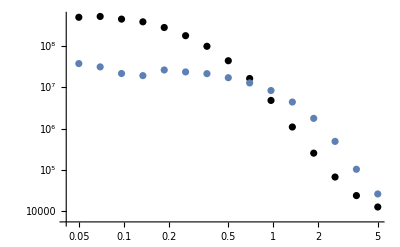

```mathematica
Show[ListLogLogPlot[dracodata, PlotStyle->Black],ListLogLogPlot[fornacdata]]
```

```mathematica
(***********************)
(******** Draco ********)
(**** Interpolation ****)
(*** / Extrapolation ***)
(***********************)
```

```mathematica
DracoInterp=Interpolation[dracodata,InterpolationOrder->2,Method-> "Spline"];
b0DracoFar=(Log[3.598428365005758245]Log[DracoInterp[5.000000000000000888]]-Log[5.000000000000000888]Log[DracoInterp[3.598428365005758245]])/(Log[3.598428365005758245]-Log[5.000000000000000888]);
msDracoFar=(Log[DracoInterp[3.598428365005758245]]-b0DracoFar)/Log[3.598428365005758245];
extrapDracoFar[x_]:=ⅇ^b0DracoFar x^msDracoFar;
b0DracoNear=(Log[4.999999999999999584 10^-2]Log[DracoInterp[9.653488644416247100 10^-2]]-Log[9.653488644416247100 10^-2]Log[DracoInterp[4.999999999999999584 10^-2]])/(Log[4.999999999999999584 10^-2]-Log[9.653488644416247100 10^-2]);
msDracoNear=(Log[DracoInterp[4.999999999999999584 10^-2]]-b0DracoNear)/Log[4.999999999999999584 10^-2];
extrapDracoNear[x_]:=ⅇ^b0DracoNear x^msDracoNear
```

```mathematica
(***********************)
(******* Fornac ********)
(**** Interpolation ****)
(*** / Extrapolation ***)
(***********************)
```

```mathematica
FornacInterp=Interpolation[fornacdata,InterpolationOrder->1,Method->"Spline"];
b0FornacFar=(Log[3.598428365005758245]Log[FornacInterp[5.000000000000000888]]-Log[5.000000000000000888]Log[FornacInterp[3.598428365005758245]])/(Log[3.598428365005758245]-Log[5.000000000000000888]);
msFornacFar=(Log[FornacInterp[3.598428365005758245]]-b0FornacFar)/Log[3.598428365005758245];
extrapFornacFar[x_]:=ⅇ^b0FornacFar x^msFornacFar;
b0FornacNear=(Log[4.999999999999999584 10^-2]Log[FornacInterp[6.947477471865685927 10^-2]]-Log[6.947477471865685927 10^-2]Log[FornacInterp[4.999999999999999584 10^-2]])/(Log[4.999999999999999584 10^-2]-Log[6.947477471865685927 10^-2]);
msFornacNear=(Log[FornacInterp[4.999999999999999584 10^-2]]-b0FornacNear)/Log[4.999999999999999584 10^-2];
extrapFornacNear[x_]:=ⅇ^b0FornacNear x^msFornacNear
```

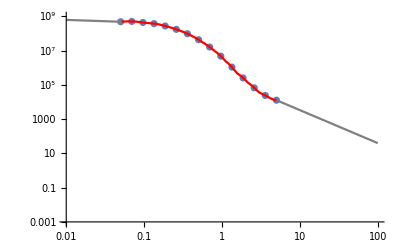

```mathematica
Show[ListLogLogPlot[dracodata,PlotRange->{{0.01,10^2},{10^-3,10^9}}], LogLogPlot[DracoInterp[r],{r,0.05,5},PlotStyle->Red],LogLogPlot[extrapDracoFar[r],{r,5,10^2},PlotStyle->Gray],LogLogPlot[extrapDracoNear[r],{r,0.01,0.05155},PlotStyle->Gray]]
```

```mathematica
DracoTest[r_]:=Piecewise[{{extrapDracoNear[r],r<0.05},{DracoInterp[r],0.05≤ r<5},{extrapDracoFar[r],5≤ r}}];
MDraco=4 π NIntegrate[r^2 DracoTest[r],{r,0,6.9768 10^-3}]
```

1000.02

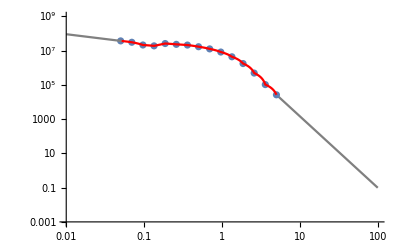

```mathematica
Show[ListLogLogPlot[fornacdata,PlotRange->{{0.01,10^2},{10^-3,10^9}}], LogLogPlot[FornacInterp[r],{r,0.05,5},PlotStyle->Red],LogLogPlot[extrapFornacFar[r],{r,5,10^2},PlotStyle->Gray],LogLogPlot[extrapFornacNear[r],{r,0.01,0.05155},PlotStyle->Gray]]
```

```mathematica
FornacTest[r_]:=Piecewise[{{extrapFornacNear[r],r<0.05},{FornacInterp[r],0.05≤ r<5},{extrapFornacFar[r],5≤ r}}];
MFornac=4 π NIntegrate[r^2 FornacTest[r],{r,0,1.3587 10^-2}]
```

1000.04

```mathematica
(***********************************)
(********* Draco Modeling **********)
(***********************************)
π 10^7 (* s/yr *);
3 10^19(* m / kpc *);
2 10^33(* g / msol *);
2 10^30(* kg / msol *);
1.8 10^-27(* kg / GeV *);
clight=2998/10^3 10^5 ; (* km /s *)
GNew=7 10^-20(1/(3 10^16))^3((2 10^30)/1)(*Newton's constant in kpc^3/(msol s^2)*);
MBH=  10^5(* Msol *);
scaleDensity=10^7.41(* Msol/ kpc^3 (0.976 GeV / cm^3)*);
scaleRadius=2.09 (* kpc *);
DracoBoundRadius=  0.0281173 (* kpc *);
FornacBoundRadius=  0.0734295;(* kpc *)
DracoannRadius=  (*10^-3*)shadowRadius  (* kpc *);
FornaxannRadius=  (*10^-3*) shadowRadius  (* kpc *);
coreRadius=0.72(* kpc *);
coreDensity=(1.(* g/cm^2 *)(1 (* msol /g *))/(2 10^33)(100 (* cm/m *))^2(3 10^19 (* m/kpc *))^2)/(10 (* km/s *)10^3(* m/km *)(1(* kpc / m*))/(3 10^19)10 (* Gyr *) 10^9(* yr/Gyr *)π 10^7(* s/yr *))(* msol / kpc^3 *);
annDensity=( 100 (* GeV *) 1.8 10^-27(* kg/GeV *) (1(* msol/kg *))/(2 10^30))/( 10^-26(* cm^3/s *) ((1(* m/cm *))/100)^3((1(* kpc/m *))/(3 10^19))^3 10 (* Gyr *)10^9(* yr/Gyr *)π 10^7(* s/yr *))(* msol / kpc^3 *);
shadowRadius=(2.GNew MBH)/((clight (* km/s *)10^3 (* m/km *)(1(* kpc/m *))/(3 10^19))^2)(* kpc *);
```

```mathematica
(*******************)
(*** Draco Spike ***)
(*******************)
DracoSpike[r_]:=NFWDraco[DracoBoundRadius](DracoBoundRadius/r)^(3/2);
ISODracoSpike[r_]:=ISODraco[DracoBoundRadius](DracoBoundRadius/r)^(3/2);
```

```mathematica
(********************)
(*** Fornac Spike ***)
(********************)
FornaxSpike[r_]:=NFWFornax[FornacBoundRadius](FornacBoundRadius/r)^(3/2);
ISOFornaxSpike[r_]:=ISOFornax[FornacBoundRadius](FornacBoundRadius/r)^(3/2);
```

```mathematica
(**************************)
(******* Draco Cusp *******)
(**************************)
DracoCusp[r_]:=extrapDracoNear[DracoBoundRadius](DracoBoundRadius/DracoannRadius)^(3/2)(DracoannRadius/r)^(1/2);
```

```mathematica
(***************)
(* Fornac Cusp *)
(***************)
FornacCusp[r_]:=extrapFornacNear[FornacBoundRadius](FornacBoundRadius/FornaxannRadius)^(3/2)(FornaxannRadius/r)^(1/2);
```

```mathematica
(**********)
(* Shadow *)
(**********)
Shadow[r_]:=0;
```

```mathematica
(*************************)
(* Draco Density Profile *)
(*************************)
DracoDensityProfile[r_]:=Piecewise[{{0,r<9.35 10^-9},{DracoSpike[r],(*DracoannRadius*)9.35 10^-9≤ r≤DracoBoundRadius },{extrapDracoNear[r],DracoBoundRadius<r≤0.05 },{DracoInterp[r],0.05<r≤5 },{extrapDracoFar[r],5<r}}];
```

```mathematica
(**************************)
(* Fornac Density Profile *)
(**************************)
FornacDensityProfile[r_]:=Piecewise[{{0,r< 3.56 10^-9},{FornacSpike[r],(*FornaxannRadius*)3.56 10^-9≤ r≤FornacBoundRadius },{extrapFornacNear[r],FornacBoundRadius<r≤0.05 },{FornacInterp[r],0.05<r≤5 },{extrapFornacFar[r],5<r}}];
```

```mathematica
4 π NIntegrate[r^2 DracoDensityProfile[r],{r,0,DracoBoundRadius}]
```

100000.

```mathematica
4 π NIntegrate[r^2 FornacDensityProfile[r],{r,0,FornacBoundRadius}]
```

100000.

```mathematica
DracoDensityProfile[9.35 10^-9]
```

2.80031×10^18

```mathematica
FornacDensityProfile[ 3.56 10^-9]
```

2.82424×10^18

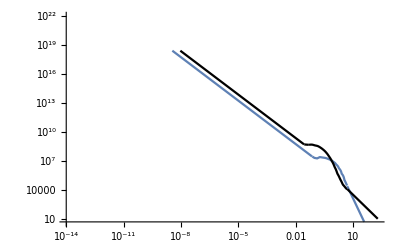

```mathematica
Show[LogLogPlot[FornacDensityProfile[r],{r,10^-13,200},PlotRange->{{10^-14,200},{5 10^0,10^22}}],LogLogPlot[DracoDensityProfile[r],{r,10^-13,200},PlotStyle->Black]]
```

```mathematica
(*********************************)
(**** Draco / Fornac J Factor ****)
(*********************************)
Dist=76;(* kpc *)
r[θ_,s_]:=√(Dist^2+s^2-2Dist s Cos[θ]);
ρDraco [θ_,s_]=DracoDensityProfile[r[θ,s]];  
ρFornac [θ_,s_]=FornacDensityProfile[r[θ,s]]; 
sMax=86; (* kpc *)
θMax=π/180(0.5);
Off[NIntegrate::inumr]
funcDraco[θ_]=NIntegrate[ρDraco[θ,s]^2,{s,66,sMax},WorkingPrecision->30];  
funcFornac[θ_]=NIntegrate[ρFornac[θ,s]^2,{s,66,sMax},WorkingPrecision->30];
```

```mathematica
plotDraco=LogPlot[funcDraco[π/180 x],{x,0,0.01 },PlotStyle-> {Black,Dotted},PlotLegends-> Placed[LineLegend[{Black,Gray},{"Draco","Fornax"},LegendLayout->"Column"],{0.8,0.8}]];
```

```mathematica
plotFornac=LogPlot[funcFornac[π/180 x],{x,0,0.01 },PlotStyle-> {Gray,Dashed}];
```

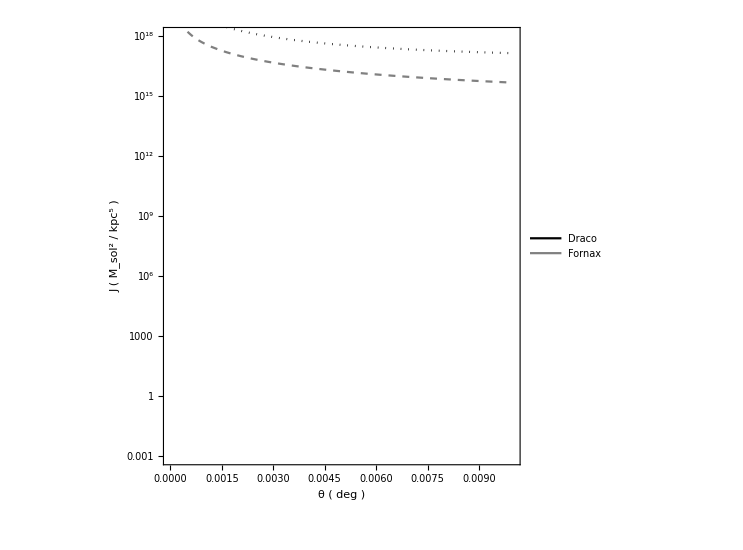

```mathematica
Show[plotDraco,plotFornac,ImageSize-> 550,Frame-> True,FrameStyle-> Directive[Thickness[0.002],Black,FontSize-> 20],FrameLabel-> {"θ ( deg )","J ( M_sol^2 / kpc^5 )"},LabelStyle->Directive[Black,FontSize-> 18],AspectRatio-> 1,PlotRange->{{10^-10,0.01},{Log[10^-3],Log[10^18]}}]
```

```mathematica
JDraco=2π NIntegrate[Sin[θ]funcDraco[θ],{θ,10^-10,θMax}] ;
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.30944×10^-8}. NIntegrate obtained 4.71702×10^12 and 5.23748×10^11 for the integral and error estimates.

```mathematica
JFornac=2π NIntegrate[Sin[θ]funcFornac[θ],{θ,10^-10,θMax}] ;
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in θ near {θ} = {1.30944×10^-8}. NIntegrate obtained 1.72751×10^12 and 2.02612×10^11 for the integral and error estimates.

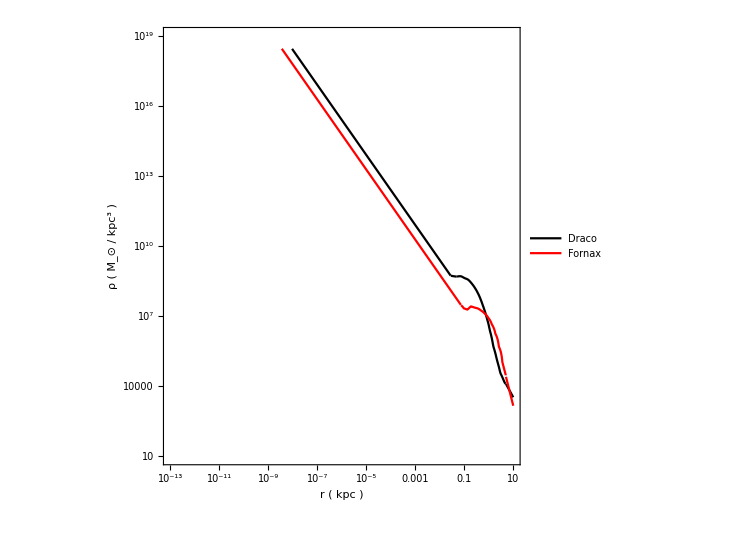

```mathematica
Show[LogLogPlot[DracoDensityProfile[r],{r,10^-13,10},PlotStyle->Black,PlotRange->{{10^-13,10},{10^1,10^19}},PlotLegends-> Placed[LineLegend[{Black,Red},{"Draco","Fornax"},LegendLayout->"Column",LabelStyle->Directive[FontSize-> 15]],{0.8,0.8}]],LogLogPlot[FornacDensityProfile[r],{r,10^-13,10},PlotStyle->Red],ImageSize-> 550,Frame-> True,FrameStyle-> Directive[Thickness[0.002],Black,FontSize-> 20],FrameLabel-> {"r ( kpc )","ρ ( M_⊙ / kpc^3 )"},LabelStyle->Directive[Black,FontSize-> 18],AspectRatio-> 1]
```

```mathematica
(* Mbh = 10^5 Msol *)
(* RcutDraco = 9.35 10^-9 kpc *)
(* RcutFornax = 3.56 10^-9 kpc *)
(* RboundaryDraco = 0.0281173 kpc *)
(* RboundaryFornax = 0.0734295 kpc *)
-Graphics-
```

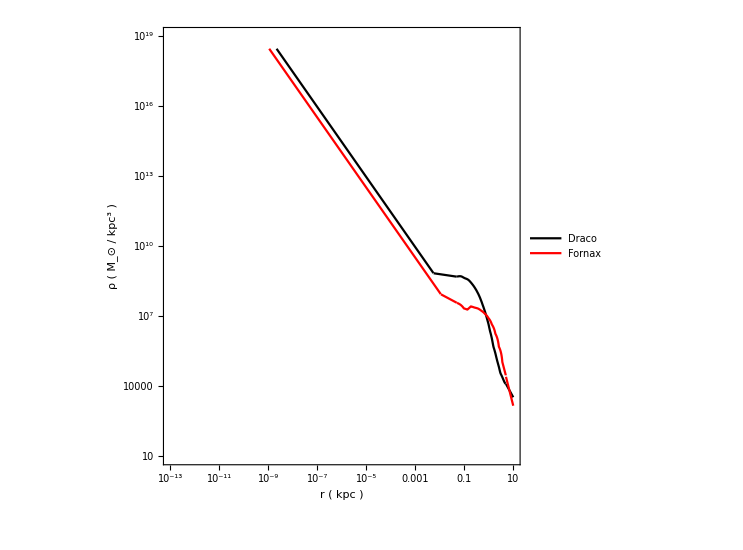
```mathematica
(* Mbh = 10^3 Msol *)
(* RcutDraco= 2.18 10^-9 kpc *)
(* RcutFornax= 1.09 10^-9 kpc *)
(* RboundaryDraco= 0.0055713 kpc *)
(* RboundaryFornax= 0.01113 kpc *)
-Graphics-
```

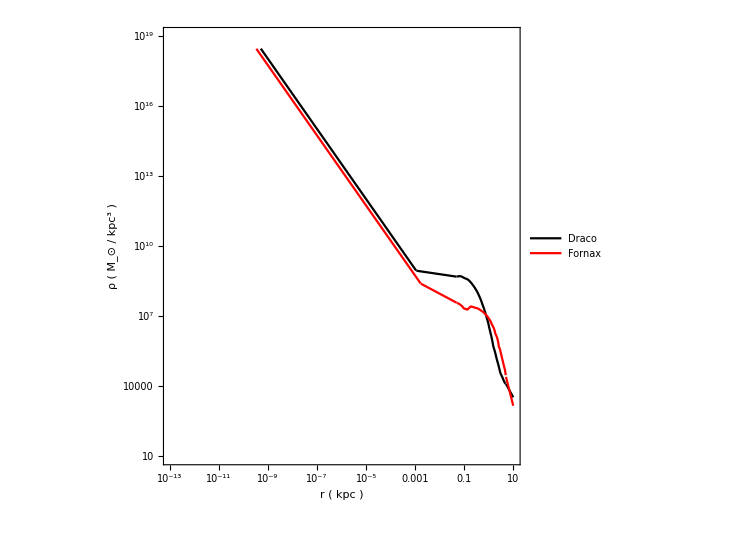

```mathematica
(* Mbh = 10 Msol *)
(* RcutDraco = 5.09 10^-10 kpc *)
(* RcutFornax = 3.35 10^-10 kpc *)
(* RboundaryDraco= 0.001107 kpc *)
(* RboundaryFornax= 0.00169 kpc *)
```

```mathematica
(* Mbh = 0 *)
```

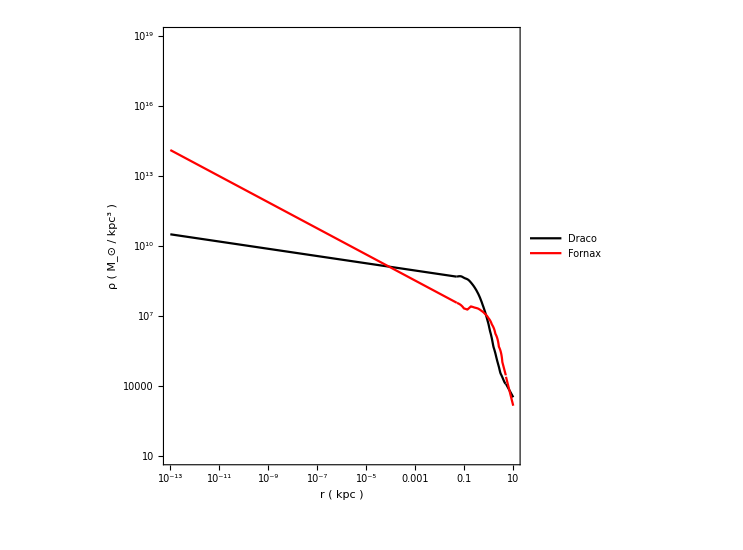

```mathematica
DracoJfactor10e5=JDraco (* Msol^2 / kpc^5 *)(1/(3 10^19(* m / kpc *)))^5(1/(10 (* cm /m *)))^5 (2 10^30(* kg / msol *))^2(1/(1.8 10^-27(* kg / GeV *)))^2
```

1.50576×10^25

```mathematica
FornaxJfactor10e5=JFornac(* Msol^2 / kpc^5 *)(1/(3 10^19(* m / kpc *)))^5(1/(10 (* cm /m *)))^5 (2 10^30(* kg / msol *))^2(1/(1.8 10^-27(* kg / GeV *)))^2
```

5.51455×10^24

```mathematica
(***************************)
(** P-Wave Xsection Limit **)
(***************************)
```

```mathematica
ϕ[x_]:=flux[x];(* gamma flux (100 MeV - 100 Gev range) cm^-2 s^-1 *)
DracoJ=DracoJfactor10e5;
FornaxJ=FornaxJfactor10e5;
ξ[x_]:=xi[x];
limitDraco[x_]:=(x^2 8 π ϕ[x])/(DracoJ ξ[x]); (* cross section limit cm^3 s^-1 *)
limitFornax[x_]:=(x^2 8 π ϕ[x])/(FornaxJ ξ[x]); (* cross section limit cm^3 s^-1 *)
```

```mathematica
step=(Log10[1000]-Log10[10])/10;
stepin= Table[10^x,{x,Log10[10],Log10[1000],step}]
```

{10,10 10^(1/5),10 10^(2/5),10 10^(3/5),10 10^(4/5),100,100 10^(1/5),100 10^(2/5),100 10^(3/5),100 10^(4/5),1000}

```mathematica
DracoXsectData10e5=Table[{i,limitDraco[i]},{i,stepin}];
DracoXsect10e5=Interpolation[DracoXsectData10e5];
FornaxXsectData10e5=Table[{i,limitFornax[i]},{i,stepin}];
FornaxXsect10e5=Interpolation[FornaxXsectData10e5];
```

InterpolatingFunction::dmval: Input value {1000} lies outside the range of data in the interpolating function. Extrapolation will be used.

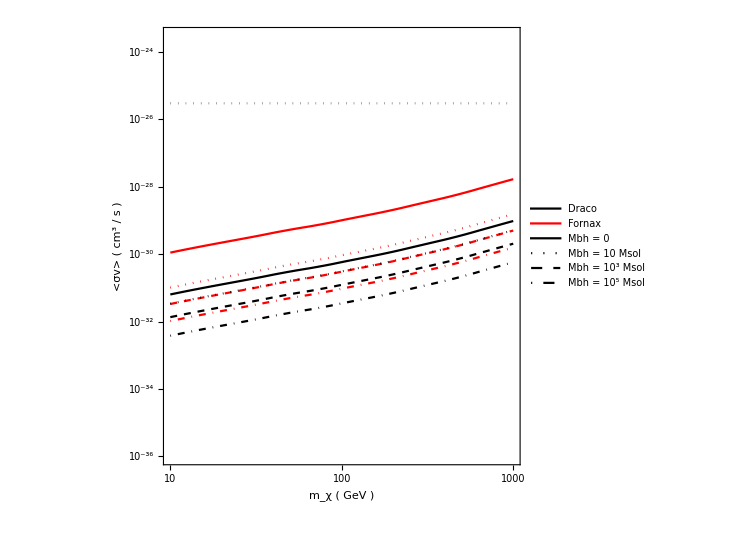

```mathematica
Show[LogLogPlot[DracoXsect10e3[x],{x,10,1000},PlotStyle->{Black,Dashed},PlotRange->{{10,1000},{10^-36,3 10^-24}},PlotLegends-> Placed[LineLegend[{Black,Red},{"Draco","Fornax"},LegendLayout->"Column",LabelStyle->Directive[FontSize-> 15]],{0.8,0.9}]],LogLogPlot[FornaxXsect10e3[x],{x,10,1000},PlotStyle->{Red,Dashed},PlotLegends-> Placed[LineLegend[{Black,Dotted,Dashed,DotDashed},{"Mbh = 0 ","Mbh = 10 Msol","Mbh = 10^3 Msol","Mbh = 10^5 Msol"},LegendLayout->"Column",LabelStyle->Directive[FontSize-> 15]],{0.3,0.83}]],LogLogPlot[DracoXsect10e5[x],{x,10,1000},PlotStyle->{Black,DotDashed}],LogLogPlot[FornaxXsect10e5[x],{x,10,1000},PlotStyle->{Red,DotDashed}],LogLogPlot[DracoXsect10e1[x],{x,10,1000},PlotStyle->{Black,Dotted}],LogLogPlot[FornaxXsect10e1[x],{x,10,1000},PlotStyle->{Red,Dotted}],LogLogPlot[DracoXsect0[x],{x,10,1000},PlotStyle->{Black}],LogLogPlot[FornaxXsect0[x],{x,10,1000},PlotStyle->{Red}],LogLogPlot[3 10^-26,{x,10,1000},PlotStyle->{Gray,Dotted}],ImageSize-> 550,Frame-> True,FrameStyle-> Directive[Thickness[0.002],Black,FontSize-> 20],FrameLabel-> {"m_χ ( GeV )","<σv> ( cm^3 / s )"},LabelStyle->Directive[Black,FontSize-> 18],AspectRatio-> 1]
```

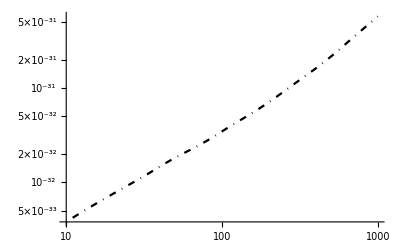

```mathematica
LogLogPlot[DracoXsect10e5[x],{x,10,1000},PlotStyle->{Black,DotDashed}]
```

```mathematica
(* DracoXsectData = {{10^-13,2.26757 10^-40},
{10^-11,2.07488 10^-37},
{10^-9,1.08385 10^-33},
{10^-7,3.66101 10^-31},
{10^-5,3.71086 10^-31},
{10^-3,3.71264 10^-31}}; *)
```

```mathematica
(* FornaxXsectData = {{10^-13,3.61534 10^-39},
{10^-11,1.73989 10^-36},
{10^-9,8.65397 10^-33},
{10^-7,5.82611 10^-30},
{10^-5,6.46964 10^-30},
{10^-3,6.47633 10^-30}}; *)
```

```mathematica
(*Show[LogLogPlot[(100 (3 10^19 10^2)^3)/((5 10^8 2 10^30 1/(1.8 10^-27))(10 10^9 π 10^7))(x/DracoBoundRadius)^(3/2),{x,10^-13,10^-3},PlotStyle->Black, PlotRange->{{10^-14,10^-4},{10^-41,10^-18}}],ListLogLogPlot[DracoXsectData]] *)
```

```mathematica
(* Show[LogLogPlot[(100 (3 10^19 10^2)^3)/((4 10^7 2 10^30 1/(1.8 10^-27))(10 10^9 π 10^7))(x/FornacBoundRadius)^(3/2),{x,10^-13,10^-3},PlotStyle->Black, PlotRange->{{10^-14,10^-4},{10^-39,10^-18}}],ListLogLogPlot[FornaxXsectData]] *)
```

```mathematica
fluxdata={{6.7876,7.6530 10^-10},
{8.6395,6.9424 10^-10},
{10.997,6.1664 10^-10},
{13.997,5.5011 10^-10},
{17.816,4.8460 10^-10},
{22.677,4.2123 10^-10},
{28.864,3.6158 10^-10},
{36.739,3.1113 10^-10},
{46.763,2.6795 10^-10},
{59.522,2.2197 10^-10},
{75.762,1.8838 10^-10},
{96.434,1.6071 10^-10},
{122.74,1.3710 10^-10},
{156.23,1.1674 10^-10},
{198.86,1.0249 10^-10},
{253.12,9.1609 10^-11},
{322.18,8.1695 10^-11},
{410.08,7.4340 10^-11},
{521.97,6.9442 10^-11},
{664.39,6.4797 10^-11},
{845.66,6.0553 10^-11},
{979.47,5.8721 10^-11}};
flux=Interpolation[fluxdata];
```

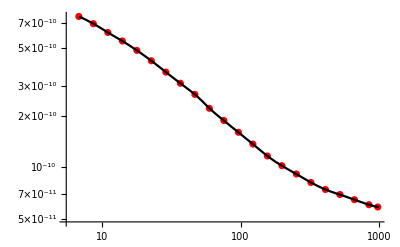

```mathematica
Show[ListLogLogPlot[fluxdata,PlotStyle->Red],LogLogPlot[flux[x],{x,6.8,1000},PlotStyle->Black]]
```

```mathematica
xidata={{10,28.4472},
{20,40.0814},
{40,53.4338},
{70,66.1692},
{100,75.4259},
{200,96.9094},
{400,124.221},
{700,150.899},
{1000,170.139}};
xi=Interpolation[xidata];
```

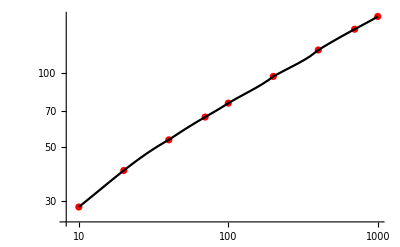

```mathematica
Show[ListLogLogPlot[xidata,PlotStyle->Red],LogLogPlot[xi[x],{x,10,1000},PlotStyle->Black]]
```

```mathematica
TestDensity={{1.22556 10^-6,2.89427 10^18 },
{1.41299 10^-6,1.95812 10^18},
{1.86098 10^-6,1.07503 10^18},
{2.43781 10^-6,5.51770 10^17},
{3.37935 10^-6,2.52902 10^17},
{4.43926 10^-6,1.35673 10^17},
{5.84672 10^-6,7.43830 10^16},
{7.57669 10^-6,4.00259 10^16},
{9.97396 10^-6,2.13634 10^16},
{1.28111 10^-5,1.16395 10^16},
{1.52171 10^-5,7.76444 10^15},
{1.74033 10^-5,5.76936 10^15},
{2.29210 10^-5,3.12192 10^15},
{3.01881 10^-5,1.59255 10^15},
{3.97592 10^-5,8.08507 10^14},
{5.23649 10^-5,4.38960 10^14},
{6.89671 10^-5,2.28963 10^14},
{9.08332 10^-5,1.23706 10^14},
{1.19632 10^-4,6.46851 10^13},
{1.57561 10^-4,3.59036 10^13},
{2.07516 10^-4,1.85741 10^13},
{2.73309 10^-4,9.61889 10^12},
{3.59961 10^-4,5.04308 10^12},
{4.59481 10^-4,2.79247 10^12},
{6.24396 10^-4,1.35756 10^12},
{8.22361 10^-4,6.94416 10^11},
{1.08309 10^-3,3.84850 10^11},
{1.42648 10^-3,1.99095 10^11},
{1.87875 10^-3,1.03466 10^11},
{2.47441 10^-3,5.39548 10^10},
{3.18089 10^-3,2.96719 10^10},
{4.02421 10^-3,1.71314 10^10},
{5.06061 10^-3,9.98822 10^9},
{7.03131 10^-3,7.59973 10^9},
{9.36737 10^-3,5.85837 10^9},
{1.27259 10^-2,4.24624 10^9},
{1.68314 10^-2,3.17309 10^9},
{2.23034 10^-2,2.32074 10^9},
{2.97607 10^-2,1.76097 10^9},
{3.99618 10^-2,1.31207 10^9},
{5.32308 10^-2,9.62092 10^8},
{7.25032 10^-2,7.05538 10^8},
{1.04800 10^-1,4.52486 10^8},
{1.38753 10^-1,3.41437 10^8},
{1.85211 10^-1,2.43277 10^8},
{2.45012 10^-1,1.81838 10^8},
{3.69332 10^-1,1.03495 10^8},
{5.91005 10^-1,5.55195 10^7},
{8.40084 10^-1,3.25137 10^7},
{1.11074,1.99649 10^7},
{1.45741,1.25048 10^7},
{2.03462,6.74987 10^6},
{2.87906,3.31130 10^6},
{4.02355,1.59472 10^6},
{5.60942,7.10847 10^5},
{7.71591,3.29994 10^5},
{9.66175,1.70376 10^5}};
DensityTest=Interpolation[TestDensity];
```

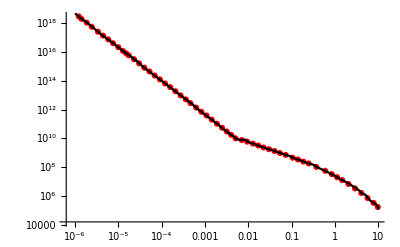

```mathematica
Show[ListLogLogPlot[TestDensity,PlotStyle->Red],LogLogPlot[DensityTest[x],{x, 10^-6,10},PlotStyle->Black]]
```

```mathematica
(****************************)
(***** Updated Profiles *****)
(*********** ISO ************)
(****************************)
G=7 10^-20(1/(3.086 10^16))^3((2 10^30)/1);(*Newton's constant in kpc^3/(msol s^2)*)
VmaxDracoIso=10^1.343(1/(3.086 10^16)); (* kpc/s *)
RmaxDracoIso=10^0.0266; (* kpc *)
v0Draco=0.630 VmaxDracoIso;
rho0Draco=(2.556 VmaxDracoIso^2)/(G RmaxDracoIso^2);
a0Draco=(4π G)/v0Draco^2 rho0Draco;
VmaxFornaxIso=10^1.371(1/(3.086 10^16)); (* kpc/s *)
RmaxFornaxIso=10^0.3455;(* kpc *)
v0Fornax=0.630 VmaxFornaxIso;
rho0Fornax=(2.556 VmaxFornaxIso^2)/(G RmaxFornaxIso^2);
a0Fornax=(4π G)/v0Fornax^2 rho0Fornax;
solDraco=NDSolve[{f''[y]+2/y f'[y]+a0Draco/(1-y)^4 ⅇ^f[y]==0,f[10^-10]==0,f'[10^-10]==0 },f,{y,10^-10,4000},PrecisionGoal->20,AccuracyGoal->20,WorkingPrecision->60,MaxSteps->Infinity,Method->"StiffnessSwitching"]
solFornax=NDSolve[{f''[y]+2/y f'[y]+a0Fornax/(1-y)^4 ⅇ^f[y]==0,f[10^-10]==0,f'[10^-10]==0 },f,{y,10^-10,4000},PrecisionGoal->20,AccuracyGoal->20,WorkingPrecision->60,MaxSteps->Infinity,Method->"StiffnessSwitching"]
```

NDSolve::precw: The precision of the differential equation ({{(71.5961 ⅇ^(f(y)))/(1+Times[«2»])^4+(2 f'(y))/y+f''(y)==0,f(1/10000000000)==0,f'(1/10000000000)==0},{},{},{},{}}) is less than WorkingPrecision (60.).

NDSolve::ndsz: At y == 0.999999999999999999999999999999999999999999999999999999184971, step size is effectively zero; singularity or stiff system suspected.

{{f→InterpolatingFunction[…]}}

NDSolve::precw: The precision of the differential equation ({{(16.485 ⅇ^(f(y)))/(1+Times[«2»])^4+(2 f'(y))/y+f''(y)==0,f(1/10000000000)==0,f'(1/10000000000)==0},{},{},{},{}}) is less than WorkingPrecision (60.).

NDSolve::ndsz: At y == 0.999999999999999999999999999999999999999999999999999974660798, step size is effectively zero; singularity or stiff system suspected.

{{f→InterpolatingFunction[…]}}

3.60206

```mathematica
ISOdataDraco=Table[{10^i,Extract[(rho0Draco ⅇ^f[10^i/(1+10^i)]/.solDraco),1]},{i,-10+Log[10,1.2],Log[10,4000],(Log[10,4000]-(-10+Log[10,1.2]))/100}];
ISODraco=Interpolation[ISOdataDraco,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
ISOdataFornax=Table[{10^i,Extract[(rho0Fornax ⅇ^f[10^i/(1+10^i)]/.solFornax),1]},{i,-10+Log[10,1.2],Log[10,4000],(Log[10,4000]-(-10+Log[10,1.2]))/100}];
ISOFornax=Interpolation[ISOdataFornax,InterpolationOrder->1]
```

InterpolatingFunction[…]

```mathematica
(************************)
(********* NFW **********)
(************************)
VmaxDraco=10^1.434(1/(3.086 10^16));(* kpc/s *)
RmaxDraco=10^0.6230; (* kpc *)
rhosDraco=(1.721 VmaxDraco^2)/(G RmaxDraco^2);
rsDraco=0.462RmaxDraco;
NFWDraco[r_]:=rhosDraco/(r/rsDraco(1+r/rsDraco)^2);
VmaxFornax=10^1.430(1/(3.086 10^16)); (* kpc/s *)
RmaxFornax=10^0.7928; (* kpc *)
rhosFornax=(1.721 VmaxFornax^2)/(G RmaxFornax^2);
rsFornax=0.462RmaxFornax;
NFWFornax[r_]:=rhosFornax/(r/rsFornax(1+r/rsFornax)^2);
```

```mathematica
(***********************)
(********* CUT *********)
(***********************)
rTidalDraco=10^1.019;(* kpc *)
CUTDraco[r_]=NFWDraco[rTidalDraco](rTidalDraco/r)^5;
rTidalDracoIso=10^1.319;(* kpc *)
CUTDracoIso[r_]=ISODraco[rTidalDracoIso](rTidalDracoIso/r)^5;
rTidalFornax=10^0.972; (* kpc *)
CUTFornax[r_]=NFWFornax[rTidalFornax](rTidalFornax/r)^5;
rTidalFornaxIso=10^1.139; (* kpc *)
CUTFornaxIso[r_]=ISOFornax[rTidalFornaxIso](rTidalFornaxIso/r)^5;
```

```mathematica
ProfileDraco[r_]:=Piecewise[{{0,r< 3.56 10^-9},{DracoSpike[r],(*FornaxannRadius*)3.56 10^-9≤ r≤DracoBoundRadius },{NFWDraco[r],DracoBoundRadius<r≤rTidalDraco },{CUTDraco[r],rTidalDraco<r}}];
ProfileFornax[r_]:=Piecewise[{{0,r< 3.56 10^-9},{FornaxSpike[r],(*FornaxannRadius*)3.56 10^-9≤ r≤FornacBoundRadius },{NFWFornax[r],FornacBoundRadius<r≤rTidalFornax },{CUTFornax[r],rTidalFornax<r}}];
```

```mathematica
ISOProfileDraco[r_]:=Piecewise[{{0,r< 3.56 10^-9},{ISODracoSpike[r],(*FornaxannRadius*)3.56 10^-9≤ r≤DracoBoundRadius },{ISODraco[r],DracoBoundRadius<r≤rTidalDracoIso },{CUTDracoIso[r],rTidalDracoIso<r}}];
ISOProfileFornax[r_]:=Piecewise[{{0,r< 3.56 10^-9},{ISOFornaxSpike[r],(*FornaxannRadius*)3.56 10^-9≤ r≤FornacBoundRadius },{ISOFornax[r],FornacBoundRadius<r≤rTidalFornaxIso},{CUTFornaxIso[r],rTidalFornaxIso<r}}];
```

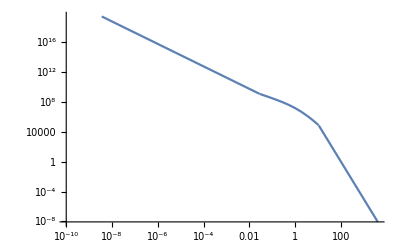

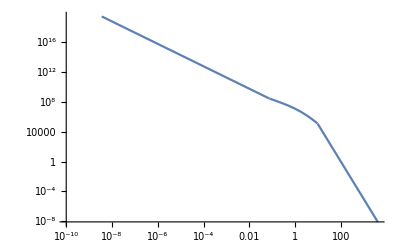

```mathematica
LogLogPlot[ProfileDraco[r],{r,10^-10,4000}]
LogLogPlot[ProfileFornax[r],{r,10^-10,4000}]
```

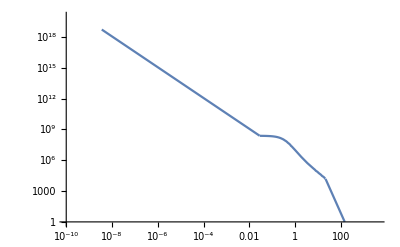

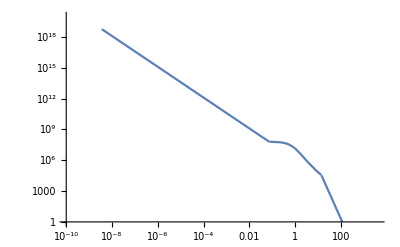

```mathematica
LogLogPlot[ISOProfileDraco[r],{r,10^-10,4000},PlotRange->{{10^-10,4000},{10^0,10^20}}]
LogLogPlot[ISOProfileFornax[r],{r,10^-10,4000},PlotRange->{{10^-10,4000},{10^0,10^20}}]
```